## Initialization

```mathematica
AppendTo[$Path, NotebookDirectory[]];
<<ColorSpacePackage`
```

Piecewise::pairs: The first argument pFun_ of Piecewise is not a list of pairs.

```mathematica
getColorSpectrumPrimative[colorData_,{min_,max_}]:=
Function[{corners},Evaluate[Raster[List[Table[List@@colorData[λ],{λ,min,max}]],corners]]]
```

```mathematica
Clear[showSpectrumResponse]
showSpectrumResponse[spectrum_,specOpts___]:=Show[DensityPlot[x, {x, 380, 720}, {y, 0, Max[{spectrum[1,specOpts][[All,2]],spectrum[2,specOpts][[All,2]],spectrum[3,specOpts][[All,2]]}]}, ColorFunction -> ColorData["VisibleSpectrum"], ColorFunctionScaling -> False, 
   AspectRatio -> 1], 
  Plot[{spectrum[1, "Func",specOpts][λ], spectrum[2, "Func",specOpts][λ], spectrum[3, "Func",specOpts][λ]}, 
   {λ, 380, 720}, PlotRange -> All, ColorFunction -> (spectrum["ColorFunction",specOpts][#1] & ), 
   ColorFunctionScaling -> False, PlotStyle -> {Directive[Thick, Red], Directive[Thick, Green], Directive[Thick, Blue]}, 
   Filling -> Axis], 
Plot[{spectrum[1, "Func",specOpts][λ], spectrum[2, "Func",specOpts][λ], spectrum[3, "Func",specOpts][λ]}, 
   {λ, 380, 720}, PlotRange -> All, PlotStyle -> {Directive[Thick, Darker[Red]], Directive[Thick, Darker[Green]], Directive[Thick, Darker[Blue]]}],
ListPlot[{spectrum[1,specOpts], spectrum[2,specOpts], spectrum[3,specOpts]}, PlotRange -> All, 
   PlotStyle -> {Red, Green, Blue}],FrameLabel->{{"Response",None},{"λ     nm" ,spectrum["name",specOpts]}},ImageSize->400]
```

```mathematica
SpectrumStrips[spectrum_,specOpts___]:=Module[{min,max,yVals,ticks},
min=0;max=Length[spectrum];
yVals=Table[i,{i,min,max,(max-min)/Length[spectrum]}];ticks=Table[{(yVals[[j]]+ yVals[[j+1]])/2,ToString[spectrum[[j]]]},{j,1,Length[spectrum],1}];Show[Table[DensityPlot[x, {x, 380, 720}, {y, yVals[[i]], yVals[[i+1]]}, ColorFunction -> spectrum[[i]]["ColorFunction",specOpts], ColorFunctionScaling -> False, 
   AspectRatio -> 1,PlotRange->{{380,720},{min,max}},FrameTicks->{ {ticks,{}},{Automatic,None}},FrameLabel->{{None,None},{"λ     nm",None}}],{i,1,Length[spectrum],1}],ImageSize->700]]
```

### Visualize Spectrums

```mathematica
Clear[PlotSpectrum]
grids[min_,max_]:=Block[{},griddid=FindDivisions[{min,max},10];griddid]
Options[PlotSpectrum]={Position->"Right",Compose-> "Overlay"};
PlotSpectrum[spectrum_,n_: 2,opts:OptionsPattern[]]:=Block[{color,pad,spectrumRange,axisLeft,axisBottom,title},w={0,0,0};h={0,0,0};ratio={0,0,0};plt={0,0,0};
pad={{1,0},{30,30}};
imgSize=500;
w=imgSize+pad[[1,1]]+pad[[1,2]];
h=(imgSize/GoldenRatio+pad[[2,1]]+pad[[2,2]]);
ratio=h/w;
If[unit=QuantityUnit[spectrum["quantityData"][[1,n]]];
TrueQ[unit=="DimensionlessUnit"],axisLeftA=Row[{spectrum["value"][[n]]}];
axisLeftB=Row[{spectrum["symbol"][[n]]}],axisLeftA=Row[{spectrum["value"][[n]]}];
axisLeftB=Row[{spectrum["symbol"][[n]],"  ",QuantityForm[unit,"Abbreviation"]}]];
If[unit=QuantityUnit[spectrum["quantityData"][[1,1]]];
TrueQ[unit=="DimensionlessUnit"],axisBottom=Row[{spectrum["symbol"][[1]]}],axisBottom=Row[{spectrum["value"][[1]],"  ",spectrum["symbol"][[1]],"  ",QuantityForm[unit,"Abbreviation"]}]];
title=Row[{spectrum["value"][[n]]," for ",spectrum["chemical"]}];
plt=ListLinePlot[QuantityMagnitude[spectrum["quantityData"][[All,{1,n}]]],PlotRange->All,Frame->True,AxesLabel->Automatic,FrameLabel->{{None,None},{axisBottom,Style[spectrum["chemical"],FontSize->14,FontFamily->"Helvetica"]}},ColorFunction->(ColorData["VisibleSpectrum"][#]&),ColorFunctionScaling->False,Filling->Axis,TargetUnits->{"Nanometers",Automatic},Evaluate[FilterRules[{opts},Options[ListLinePlot]]],ImageSize->{w,h},ImagePadding->pad,ImageMargins->0,GridLines->{None,None},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}}];

pltRange=PlotRange/.AbsoluteOptions[plt,PlotRange];
griddid=N[FindDivisions[{pltRange[[2,1]],pltRange[[2,2]]},10]];
axisScaled[{x_,y_}]:={(pltRange[[1,2]]-pltRange[[1,1]]) x+pltRange[[1,1]],(pltRange[[2,2]]-pltRange[[2,1]]) y+pltRange[[2,1]]};
If[TrueQ[OptionValue[Position]=="Right"],eplg=Flatten[{Map[Inset[Style[#,Background->White],{pltRange[[1,1]],#},{Left,Center}]&,griddid],Map[Inset[Style[#,Background->White],{(pltRange[[1,1]]+pltRange[[1,2]])/2,#},{Center,Center}]&,griddid],Map[Inset[Style[#,Background->White],{pltRange[[1,2]],#},{Right,Center}]&,griddid],Inset[Pane[Column[{Style[axisLeftA,FontSize->20,FontFamily->"Helvetica",Bold,FontTracking->"Wide",Opacity[0.6]],Style[axisLeftB,FontSize->14,FontFamily->"Helvetica",Bold,FontTracking->"Wide",Opacity[0.6]]},Alignment->Center],ImageSizeAction->"ResizeToFit"],axisScaled[{0.85,0.5}],{Center,Center},Automatic,{0,1}]}],eplg=Flatten[{Map[Inset[Style[#,Background->White],{pltRange[[1,1]],#},{Left,Center}]&,griddid],Map[Inset[Style[#,Background->White],{(pltRange[[1,1]]+pltRange[[1,2]])/2,#},{Center,Center}]&,griddid],Map[Inset[Style[#,Background->White],{pltRange[[1,2]],#},{Right,Center}]&,griddid],Inset[Pane[Column[{Style[axisLeftA,FontSize->20,FontFamily->"Helvetica",Bold,FontTracking->"Wide",Opacity[0.6]],Style[axisLeftB,FontSize->14,FontFamily->"Helvetica",Bold,FontTracking->"Wide",Opacity[0.6]]},Alignment->Center],ImageSizeAction->"ResizeToFit"],axisScaled[{0.15,0.5}],{Center,Center},Automatic,{0,1}]}]];
pltBg=ListLinePlot[QuantityMagnitude[spectrum["quantityData"][[All,{1,n}]]],PlotRange->All,Frame->True,FrameLabel->{{None,None},{axisBottom,Style[spectrum["chemical"],FontSize->14,FontFamily->"Helvetica"]}},PlotStyle->White,TargetUnits->{"Nanometers",Automatic},ImageSize->{w,h},ImagePadding->pad,ImageMargins->0,GridLines->{None,grids},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},Epilog->eplg];
If[TrueQ[OptionValue[Compose]=="Overlay"],
Overlay[{pltBg,plt}],
ImageCompose[Rasterize[pltBg,ImageResolution->600,ImageSize->imgSize],Rasterize[plt,ImageResolution->600,ImageSize->imgSize,Background->None]]
]
]
```

### Export Functions

```mathematica
FigsPath="Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/";
ExportPanel[out_,fileName_]:=Module[{},Panel[Column[{Panel[out,Background->White],
Button["Export EPS",Export[fileName<>".eps",out,"EPS"]],
Button["Export JPG",Export[fileName<>".jpg",out,"JPG",ImageResolution->300]]}]]
];
```

## A possible axis style?

```mathematica
spectrumAxis[{min_,max_}]:=Block[{λTicks,colorSpectrumPrimative},λTicks=Select[FindDivisions[{min,max},10],(#>min&&#<max)&];
colorSpectrumPrimative=getColorSpectrumPrimative[ColorData["VisibleSpectrum"],{min,max}];Graphics[{Opacity[1],colorSpectrumPrimative[{{min,-10},{max,0}}],Black,Table[sequence[Line[{{λ,-12},{λ,2}}],Text[ToString[λ],{λ,-14},{1,0.5},{0,1}]],{λ,λTicks}]/.sequence->Sequence,
Text["Wavelength λ nm",{(max+min)/2,-30},{Center,Center}]},AlignmentPoint->{min,0},ImageSize->300,PlotRangePadding->0]];
```

```mathematica
AddSpectralAxis[plt_]:=Block[{pltRange},
pltRange=PlotRange/.AbsoluteOptions[plt,PlotRange];
Show[plt,Epilog-> {Inset[spectrumAxis[{pltRange[[1,1]],pltRange[[1,2]]}],{pltRange[[1,1]],0},{Left,2},pltRange[[1,2]]-pltRange[[1,1]]],},PlotRangeClipping->False]]
```

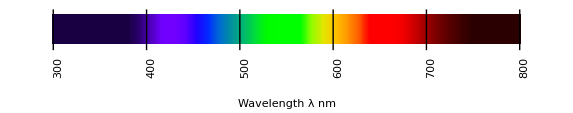

```mathematica
spectrumAxis[{299,801}]
```

```mathematica
plt=Plot[{physical[1, "Func"][λ], physical[2, "Func"][λ], physical[3, "Func"][λ]}, 
   {λ, 380, 750}, PlotRange -> All, PlotStyle -> {Directive[Thick, Red], Directive[Thick, Green], Directive[Thick, Blue]},Frame->True,FrameTicks->{{Automatic,None},{None,Automatic}},AlignmentPoint->{380,0},ImageSize->500,ImagePadding->{{1,1},{30,1}}];
```

```mathematica
plot=Plot[{physical[1, "Func"][λ], physical[2, "Func"][λ], physical[3, "Func"][λ]}, 
   {λ, 380, 750}, PlotRange -> All,ColorFunction -> (physical["ColorFunction"][#1] & ), Filling->Axis,
   ColorFunctionScaling -> False, PlotStyle -> {Directive[Thick, Red], Directive[Thick, Green], Directive[Thick, Blue]},Frame->True,FrameTicks->{{Automatic,None},{None,Automatic}},AlignmentPoint->{380,0},ImageSize->500,ImagePadding->{{1,1},{40,1}}];
```

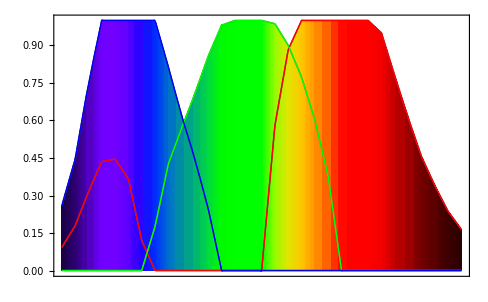

```mathematica
Show[{AddSpectralAxis[plot],plt}]
```

## Stuff

```mathematica
AbsOxyHemo = Import["AbsorbanceOxyHemo.csv"];
AbsDeOxyHemo = Import["AbsorbanceDeOxyHemo.csv"];
AbsMel= Import["AbsorbanceMel.csv"];
```

```mathematica
showSpectrumResponse[spectrum_]:=Show[DensityPlot[x, {x, 380, 720}, {y, 0, 1}, ColorFunction -> ColorData["VisibleSpectrum"], ColorFunctionScaling -> False, 
   AspectRatio -> 1], 
  Plot[{spectrum[1, "Func"][λ], spectrum[2, "Func"][λ], spectrum[3, "Func"][λ]}, 
   {λ, 380, 720}, PlotRange -> All, ColorFunction -> (spectrum["ColorFunction"][#1] & ), 
   ColorFunctionScaling -> False, PlotStyle -> {Directive[Thick, Red], Directive[Thick, Green], Directive[Thick, Blue]}, 
   Filling -> Axis], 
Plot[{spectrum[1, "Func"][λ], spectrum[2, "Func"][λ], spectrum[3, "Func"][λ]}, 
   {λ, 380, 720}, PlotRange -> All, PlotStyle -> {Directive[Thick, Darker[Red]], Directive[Thick, Darker[Green]], Directive[Thick, Darker[Blue]]}],
ListPlot[{spectrum[1], spectrum[2], spectrum[3]}, PlotRange -> All, 
   PlotStyle -> {Red, Green, Blue}],FrameLabel->{{"Response",None},{"λ     nm" ,spectrum["name"]}},ImageSize->400]
```

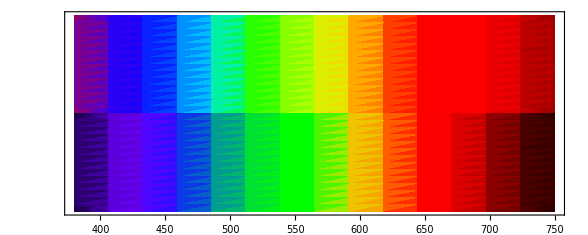

```mathematica
Show[DensityPlot[x,{x,380,750},{y,25,50},ColorFunction->(RGBColor@@toRGB[#1]&),ColorFunctionScaling->False,PlotRange->{All,{0,50}}],DensityPlot[x,{x,380,750},{y,0,25},ColorFunction->ColorData["VisibleSpectrum"],ColorFunctionScaling->False,PlotRange->{All,{0,50}}],AspectRatio->Automatic,PlotRangePadding->10,FrameTicks->{{None,None},{Automatic,None}}]
```

```mathematica
showWavelengthColor[list_]:= 
Graphics[{EdgeForm[Gray],Table[{ColorData["VisibleSpectrum"][list[[t]]],Disk[{t,0},.4],Black,Text[list[[t]]"λ",{t,0},{-1,0},{0,1}]},{t,1,Length[list]}]}]
```

```mathematica
OxyHemoglobin={415,540,570};
DeoxyHemoglobin={430,555};
```

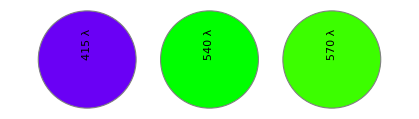

```mathematica
showWavelengthColor[OxyHemoglobin]
```

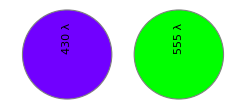

```mathematica
showWavelengthColor[DeoxyHemoglobin]
```

```mathematica
OxyHemoglobinRGB = Transpose[Map[toRGB,OxyHemoglobin]]
DeoxyHemoglobinRGB = Transpose[Map[toRGB,DeoxyHemoglobin]]
```

{{0.158333,3/7,6/7},{0,1,1},{1,0,0}}

{{0.0633333,9/14},{0,1},{1,0}}

```mathematica
nYAB[-0.1537].OxyHemoglobinRGB + {{0,0,0},{0.5,0.5,0.5},{0.5,0.5,0.5}}
```

{{0.193056,0.238095,0.309524},{0.846045,0.0783929,0.156786},{0.161267,0.632185,0.846471}}

## Response Spectra

```mathematica
ResponseSpectra={};
```

### Physical Spectrum

```mathematica
toRGB[wavelength_]:=Piecewise[{{{0.6 - 0.41(wavelength-380)/30,0,0.39 + 0.6(wavelength-380)/30},wavelength ≥ 380.0 && wavelength ≤ 410.0},{{0.19 - 0.19(wavelength-410)/30,0,1},wavelength ≥ 410.0 && wavelength ≤ 440.0},{{0,1 - (490-wavelength)/50,1},wavelength ≥ 440.0 && wavelength ≤ 490.0},{{0,1,(510-wavelength)/20},wavelength ≥ 490.0 && wavelength ≤ 510.0},{{1 - (580-wavelength)/70,1,0},wavelength ≥ 510.0 && wavelength ≤ 580.0},
{{1,(640-wavelength)/60,0},wavelength ≥ 580.0 && wavelength ≤ 640.0},
{{1,0,0},wavelength ≥ 640.0 && wavelength ≤ 700.0},
{{0.35 + 0.65(780-wavelength)/80,0,0},wavelength ≥ 700.0 && wavelength ≤ 780.0}}]
```

```mathematica
AppendTo[ResponseSpectra,approxPhysical]
```

{approxPhysical}

```mathematica
approxPhysical["name"]="Approximate Physical Spectrum";
Do[
approxPhysical[i,"Func"]     =Function[{λ},Evaluate[ApplyToPiecewise[#[[i]]&,toRGB[λ]]]];
approxPhysical[i,"Func","norm"]=approxPhysical[i,"Func"];
approxPhysical[i,"Func","maxNorm"]=approxPhysical[i,"Func"];
approxPhysical[i]= Table[{j,approxPhysical[i,"Func"][j]},{j,300,780}];
approxPhysical[i,"norm"]=approxPhysical[i];
approxPhysical[i,"maxNorm"]=approxPhysical[i];

,{i,1,3}];
approxPhysical["ColorFunction"]= Function[{λ},RGBColor[toRGB[λ]]];
approxPhysical["ColorFunction","norm"]=approxPhysical["ColorFunction"];
approxPhysical["ColorFunction","maxNorm"]=approxPhysical["ColorFunction"];
```

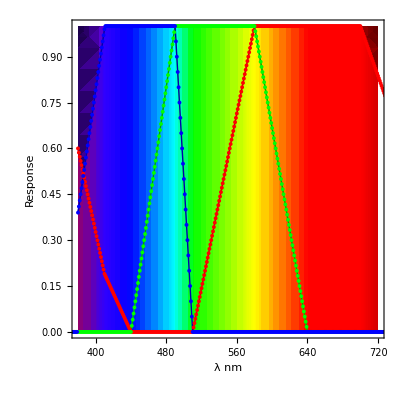

```mathematica
showSpectrumResponse[approxPhysical]
```

```mathematica
AppendTo[ResponseSpectra,physical];
```

```mathematica
physical["name"]="Physical Spectrum";
Do[
physical[i,"Func"]     =Function[{λ},(List@@ColorData["VisibleSpectrum"][λ])[[j]]]/.j->i;
physical[i]= Table[{j,physical[i,"Func"][j]},{j,300,780}];
physical[i,"Func"]=Interpolation[physical[i]];
physical[i,"Func","norm"]=physical[i,"Func"];
physical[i,"Func","maxNorm"]=physical[i,"Func"];
,{i,1,3}];

physical["ColorFunction"]= ColorData["VisibleSpectrum"];
physical["ColorFunction","norm"]=physical["ColorFunction"];
physical["ColorFunction","maxNorm"]=physical["ColorFunction"];
```

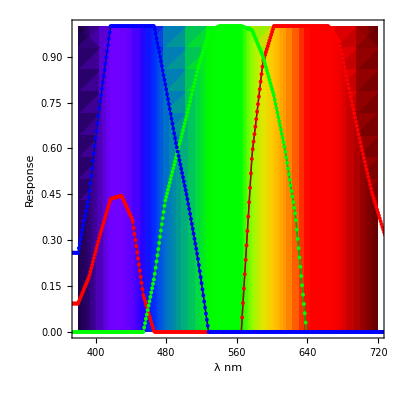

```mathematica
showSpectrumResponse[physical]
```

### The human Eye

```mathematica
AppendTo[ResponseSpectra,eye];
```

```mathematica
Clear[eye];
σRGB={60,60,60}; μRGB ={580,530,450};
gaussian[λ_,μ_,σ_]:= Exp[-(λ-μ)^2/(2*σ^2)];
eye["name"]="Response Spectrum for the human eye";
eye[3]= Import["EyeRGB_Blue_Gaussian.csv"];
eye[2]= Import["EyeRGB_Green_Gaussian.csv"];
eye[1]= Import["EyeRGB_Red_Gaussian.csv"];
Do[
{σRGB[[i]],μRGB[[i]]}={σ,μ}/.FindFit[eye[i],gaussian[λ,μ,σ],{{σ,σRGB[[i]]},{ μ, μRGB[[i]]}},λ];
eye[i,"Func"]     =Function[{λ}, Evaluate[gaussian[λ,μRGB[[i]],σRGB[[i]]]]];
eye[i,"Func","norm"]=eye[i,"Func"];
eye[i,"Func","maxNorm"]=eye[i,"Func"];
eye[i,"norm"]=eye[i];
eye[i,"maxNorm"]=eye[i];
,{i,1,3}];
eye["ColorFunction"]=RGBColor[eye[1,"Func"][#],eye[2,"Func"][#],eye[3,"Func"][#]]&;
eye["ColorFunction","norm"]=eye["ColorFunction"];
eye["ColorFunction","maxNorm"]=eye["ColorFunction"];
```

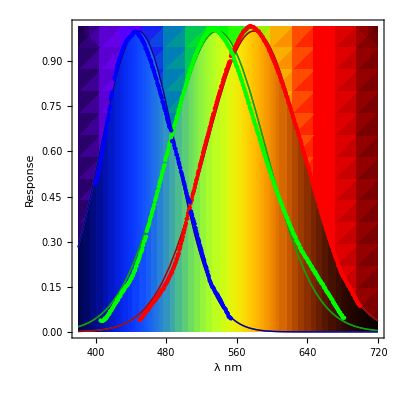

```mathematica
showSpectrumResponse[eye]
```

### Digital Camera Response Spectra

Data From www.cis.rit.edu/jwgu/research/camspec/db.php

```mathematica
camData= Import["camspec_database.csv"];
```

```mathematica
scalePoints[list_,scale_]:=Block[{tran},tran=Transpose[list];Transpose[{scale[[1]] tran[[1]],scale[[2]] tran[[2]]}]];
```

```mathematica
camspecDatabaseλ=Table[λ,{λ,400,720,10}];
```

```mathematica
Do[
sym     = ToExpression[           StringReplace[camData[[n,1]], {" " -> "","-"->""}]]; 
AppendTo[ResponseSpectra,sym];
sym["name"]     = StringJoin["Response Spectrum for the ",camData[[n,1]]];
sym["name","norm"] = StringJoin["Integral Normalized Response Spectrum for the ",camData[[n,1]]];
sym["name","maxNorm"] = StringJoin["Max Normalized Response Spectrum for the ",camData[[n,1]]];
sym["Red"]   = sym[1]; sym["Green"] = sym[2]; sym["Blue"]  = sym[3];
Do[
sym[i]       = Prepend[Prepend[Transpose[{camspecDatabaseλ,camData[[n + i]]}],{390,0}],{380,0}];
sym[i,"max"] = sym[i][[Ordering[sym[i][[All,2]],-1][[1]]]];
sym[i,"maxNorm"]   = scalePoints[sym[i],{1,1/sym[i,"max"][[2]]}];
max = FindMaximum[Interpolation[sym[i,"maxNorm"]][λ],{λ, sym[i,"max"][[1]]}];
sym[i,"Func"] = Interpolation[sym[i]];
sym[i,"Func","maxNorm"] = Interpolation[scalePoints[sym[i,"maxNorm"],{1,1/max[[1]]}]];
sym[i,"integral"]=NIntegrate[sym[i,"Func"][λ],{λ,380,720}];
,{i,1,3}]; 
reScale=Max[{sym[1,"integral"],sym[2,"integral"],sym[3,"integral"]}];
Do[
sym[i,"norm"]   = scalePoints[sym[i],{1,reScale/ sym[i,"integral"]}];
sym[i,"Func","norm"] = Interpolation[sym[i,"norm"]];
,{i,1,3}];
sym["ColorFunction"] = Function[{λ},Evaluate[RGBColor[    sym[1,"Func"][λ],    sym[2,"Func"][λ],    sym[3,"Func"][λ]]]];
sym["ColorFunction","maxNorm"] =Function[{λ},Evaluate[RGBColor[sym[1,"Func","maxNorm"][λ],sym[2,"Func","maxNorm"][λ],sym[3,"Func","maxNorm"][λ]]]];
sym["ColorFunction","norm"] =Function[{λ},Evaluate[RGBColor[sym[1,"Func","norm"][λ],sym[2,"Func","norm"][λ],sym[3,"Func","norm"][λ]]]];
 , {n, 1, Length[camData], 4}]
```

```mathematica
ResponseSpectra
```

{approxPhysical,physical,eye,Canon1DMarkIII,Canon20D,Canon300D,Canon40D,Canon500D,Canon50D,Canon5DMarkII,Canon600D,Canon60D,HasselbladH2,NikonD3X,NikonD200,NikonD3,NikonD300s,NikonD40,NikonD50,NikonD5100,NikonD700,NikonD80,NikonD90,NokiaN900,OlympusEPL2,PentaxK5,PentaxQ,PointGreyGrasshopper50S5C,PointGreyGrasshopper214S5C,PhaseOne,SONYNEX5N}

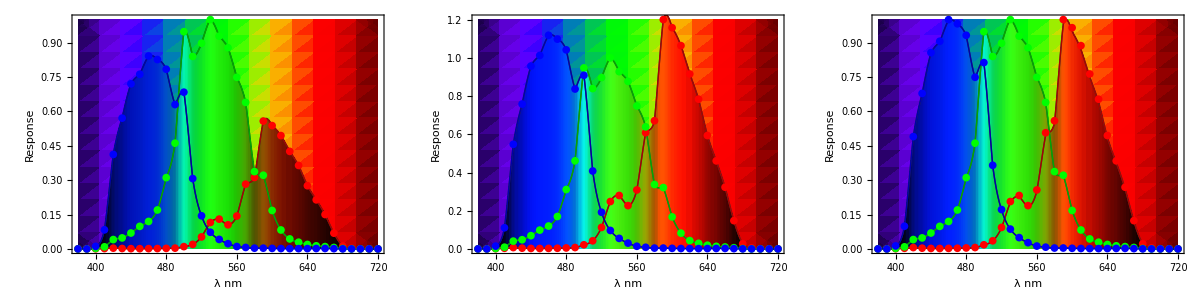

```mathematica
Grid[{{showSpectrumResponse[ResponseSpectra[[4]]],showSpectrumResponse[ResponseSpectra[[4]],"norm"],showSpectrumResponse[ResponseSpectra[[4]],"maxNorm"]}}]
```

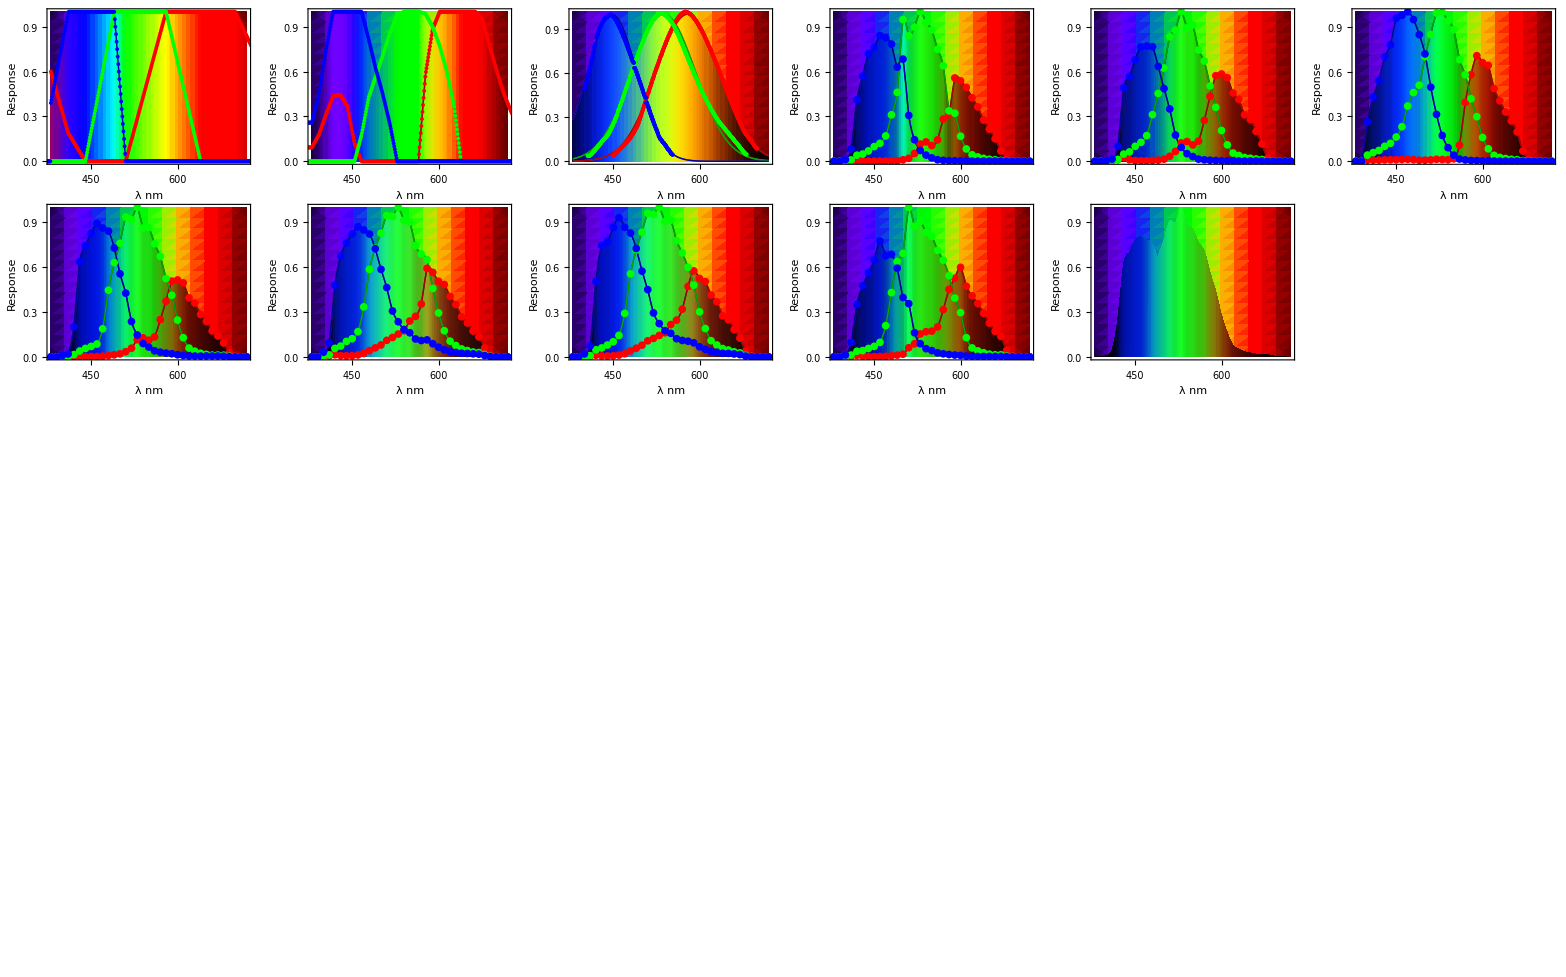

```mathematica
cameraSpectrumResponseGraphs=Table[showSpectrumResponse[ResponseSpectra[[i]]],{i,1,Length[ResponseSpectra]}];
Grid[ArrayReshape[cameraSpectrumResponseGraphs,{Floor[N[Sqrt[Length[ResponseSpectra]]]],Ceiling[N[Sqrt[Length[ResponseSpectra]]]]}]]
```

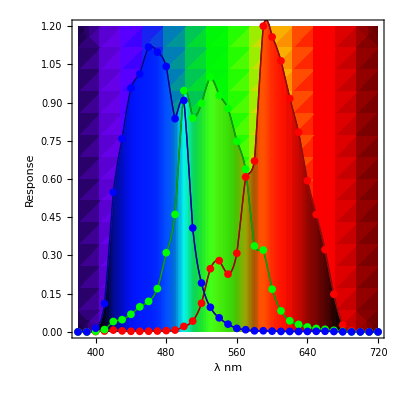
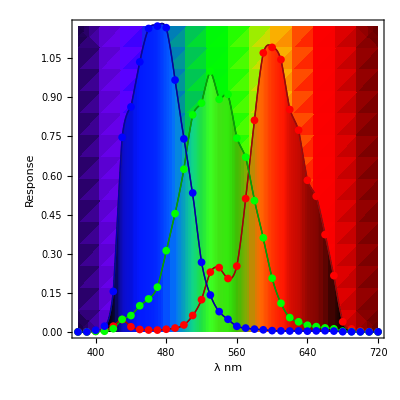
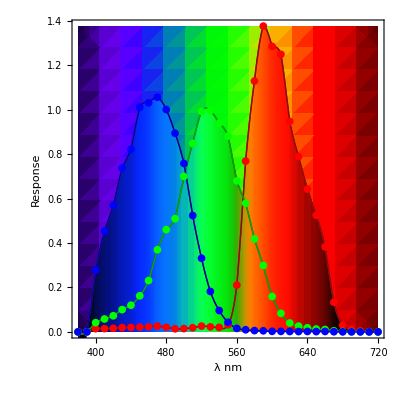
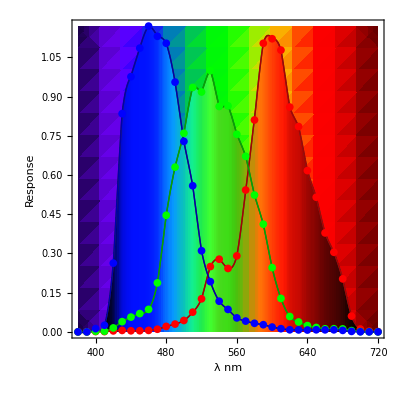
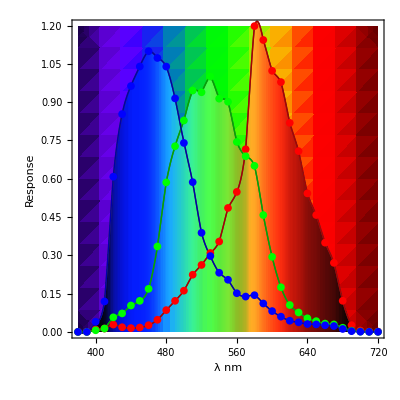
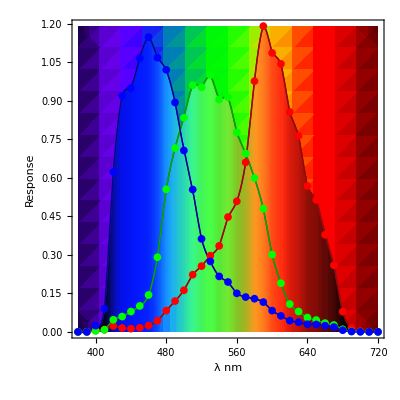
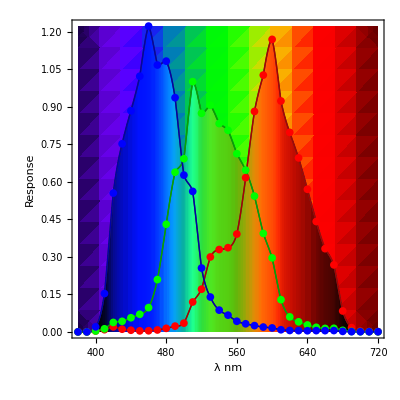
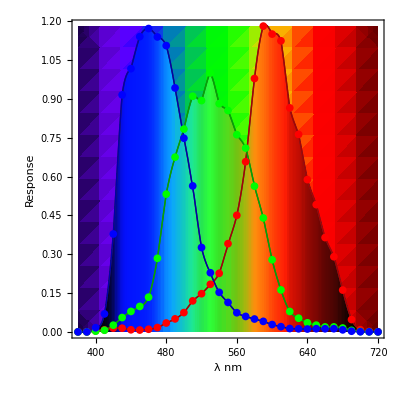
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 0

```mathematica
cameraSpectrumResponseGraphs=Table[showSpectrumResponse[ResponseSpectra[[i]],"norm"],{i,3,Length[ResponseSpectra]}];
Grid[ArrayReshape[cameraSpectrumResponseGraphs,{Floor[N[Sqrt[Length[ResponseSpectra]]]],Ceiling[N[Sqrt[Length[ResponseSpectra]]]]}]]
```

```mathematica
TabView[{"Raw"->ExportPanel[SpectrumStrips[ResponseSpectra[[1;;Length[ResponseSpectra]]]],FigsPath<>"ResponseSpectraStripes"],"Normed"->ExportPanel[SpectrumStrips[ResponseSpectra[[1;;Length[ResponseSpectra]]],"norm"],FigsPath<>"ResponseSpectraStripesNorm"],"MaxNormed"->ExportPanel[SpectrumStrips[ResponseSpectra[[3;;Length[ResponseSpectra]]],"maxNorm"],FigsPath<>"ResponseSpectraStripesmaxNorm"]}]
```

123

```mathematica
camera=NokiaN900;
Panel[Column[{
PopupMenu[Dynamic[camera],ResponseSpectra],
Dynamic[ExportPanel[GraphicsGrid[{{showSpectrumResponse[camera],showSpectrumResponse[camera,"norm"],showSpectrumResponse[camera,"maxNorm"]}},Spacings->0],FigsPath<>"ResponseSpectrum_"<>ToString[camera]]]
}]
]
```

## The Absorbtion Spectrum for Chromophores

### Chromophore Data

Data from http : // omlc.org/spectra

```mathematica
hemoglobin["base"] = 10;
hemoglobin["chemical"] = "Hb";
hemoglobin["quantity"] = {Quantity[1, "Nanometers"], Quantity[1/10, "Meters"^2/"Moles"]};
hemoglobin["symbol"] = {"λ", TraditionalForm[ε]};
hemoglobin["units"] = {"nm", TraditionalForm["l"/("cm"*"mol")]};
hemoglobin["value"] = {"Wavelength", "Molar absorptivity"};
hemoglobin["data"] = {{250, 112736}, {252, 112736}, {254, 112736}, {256, 113824}, {258, 115040}, {260, 116296}, {262, 117564}, {264, 118876}, 
     {266, 120208}, {268, 121544}, {270, 122880}, {272, 123096}, {274, 121952}, {276, 120808}, {278, 119840}, {280, 118872}, {282, 117628}, 
     {284, 114820}, {286, 112008}, {288, 107140}, {290, 98364}, {292, 91636}, {294, 85820}, {296, 77100}, {298, 69444}, {300, 64440}, 
     {302, 61300}, {304, 58828}, {306, 56908}, {308, 57620}, {310, 59156}, {312, 62248}, {314, 65344}, {316, 68312}, {318, 71208}, {320, 74508}, 
     {322, 78284}, {324, 82060}, {326, 85592}, {328, 88516}, {330, 90856}, {332, 93192}, {334, 95532}, {336, 99792}, {338, 104476}, 
     {340, 108472}, {342, 110996}, {344, 113524}, {346, 116052}, {348, 118752}, {350, 122092}, {352, 125436}, {354, 128776}, {356, 132120}, 
     {358, 133632}, {360, 134940}, {362, 136044}, {364, 136972}, {366, 137900}, {368, 138856}, {370, 139968}, {372, 141084}, {374, 142196}, 
     {376, 143312}, {378, 144424}, {380, 145232}, {382, 145232}, {384, 148668}, {386, 153908}, {388, 159544}, {390, 167780}, {392, 180004}, 
     {394, 191540}, {396, 202124}, {398, 212712}, {400, 223296}, {402, 236188}, {404, 253368}, {406, 270548}, {408, 287356}, {410, 303956}, 
     {412, 321344}, {414, 342596}, {416, 363848}, {418, 385680}, {420, 407560}, {422, 429880}, {424, 461200}, {426, 481840}, {428, 500840}, 
     {430, 528600}, {432, 552160}, {434, 552160}, {436, 547040}, {438, 501560}, {440, 413280}, {442, 363240}, {444, 282724}, {446, 237224}, 
     {448, 173320}, {450, 103292}, {452, 62640}, {454, 36170}, {456, 30698.8}, {458, 25886.4}, {460, 23388.8}, {462, 20891.2}, {464, 19260.8}, 
     {466, 18142.4}, {468, 17025.6}, {470, 16156.4}, {472, 15310}, {474, 15048.4}, {476, 14792.8}, {478, 14657.2}, {480, 14550}, {482, 14881.2}, 
     {484, 15212.4}, {486, 15543.6}, {488, 15898}, {490, 16684}, {492, 17469.6}, {494, 18255.6}, {496, 19041.2}, {498, 19891.2}, {500, 20862}, 
     {502, 21832.8}, {504, 22803.6}, {506, 23774.4}, {508, 24745.2}, {510, 25773.6}, {512, 26936.8}, {514, 28100}, {516, 29263.2}, 
     {518, 30426.4}, {520, 31589.6}, {522, 32851.2}, {524, 34397.6}, {526, 35944}, {528, 37490}, {530, 39036.4}, {532, 40584}, {534, 42088}, 
     {536, 43592}, {538, 45092}, {540, 46592}, {542, 48148}, {544, 49708}, {546, 51268}, {548, 52496}, {550, 53412}, {552, 54080}, {554, 54520}, 
     {556, 54540}, {558, 54164}, {560, 53788}, {562, 52276}, {564, 50572}, {566, 48828}, {568, 46948}, {570, 45072}, {572, 43340}, {574, 41716}, 
     {576, 40092}, {578, 38467.6}, {580, 37020}, {582, 35676.4}, {584, 34332.8}, {586, 32851.6}, {588, 31075.2}, {590, 28324.4}, {592, 25470}, 
     {594, 22574.8}, {596, 19800}, {598, 17058.4}, {600, 14677.2}, {602, 13622.4}, {604, 12567.6}, {606, 11513.2}, {608, 10477.6}, {610, 9443.6}, 
     {612, 8591.2}, {614, 7762}, {616, 7344.8}, {618, 6927.2}, {620, 6509.6}, {622, 6193.2}, {624, 5906.8}, {626, 5620}, {628, 5366.8}, 
     {630, 5148.8}, {632, 4930.8}, {634, 4730.8}, {636, 4602.4}, {638, 4473.6}, {640, 4345.2}, {642, 4216.8}, {644, 4088.4}, {646, 3965.08}, 
     {648, 3857.6}, {650, 3750.12}, {652, 3642.64}, {654, 3535.16}, {656, 3427.68}, {658, 3320.2}, {660, 3226.56}, {662, 3140.28}, 
     {664, 3053.96}, {666, 2967.68}, {668, 2881.4}, {670, 2795.12}, {672, 2708.84}, {674, 2627.64}, {676, 2554.4}, {678, 2481.16}, 
     {680, 2407.92}, {682, 2334.68}, {684, 2261.48}, {686, 2188.24}, {688, 2115}, {690, 2051.96}, {692, 2000.48}, {694, 1949.04}, {696, 1897.56}, 
     {698, 1846.08}, {700, 1794.28}, {702, 1741}, {704, 1687.76}, {706, 1634.48}, {708, 1583.52}, {710, 1540.48}, {712, 1497.4}, {714, 1454.36}, 
     {716, 1411.32}, {718, 1368.28}, {720, 1325.88}, {722, 1285.16}, {724, 1244.44}, {726, 1203.68}, {728, 1152.8}, {730, 1102.2}, {732, 1102.2}, 
     {734, 1102.2}, {736, 1101.76}, {738, 1100.48}, {740, 1115.88}, {742, 1161.64}, {744, 1207.4}, {746, 1266.04}, {748, 1333.24}, 
     {750, 1405.24}, {752, 1515.32}, {754, 1541.76}, {756, 1560.48}, {758, 1560.48}, {760, 1548.52}, {762, 1508.44}, {764, 1459.56}, 
     {766, 1410.52}, {768, 1361.32}, {770, 1311.88}, {772, 1262.44}, {774, 1213}, {776, 1163.56}, {778, 1114.8}, {780, 1075.44}, {782, 1036.08}, 
     {784, 996.72}, {786, 957.36}, {788, 921.8}, {790, 890.8}, {792, 859.8}, {794, 828.8}, {796, 802.96}, {798, 782.36}, {800, 761.72}, 
     {802, 743.84}, {804, 737.08}, {806, 730.28}, {808, 723.52}, {810, 717.08}, {812, 711.84}, {814, 706.6}, {816, 701.32}, {818, 696.08}, 
     {820, 693.76}, {822, 693.6}, {824, 693.48}, {826, 693.32}, {828, 693.2}, {830, 693.04}, {832, 692.92}, {834, 692.76}, {836, 692.64}, 
     {838, 692.48}, {840, 692.36}, {842, 692.2}, {844, 691.96}, {846, 691.76}, {848, 691.52}, {850, 691.32}, {852, 691.08}, {854, 690.88}, 
     {856, 690.64}, {858, 692.44}, {860, 694.32}, {862, 696.2}, {864, 698.04}, {866, 699.92}, {868, 701.8}, {870, 705.84}, {872, 709.96}, 
     {874, 714.08}, {876, 718.2}, {878, 722.32}, {880, 726.44}, {882, 729.84}, {884, 733.2}, {886, 736.6}, {888, 739.96}, {890, 743.6}, 
     {892, 747.24}, {894, 750.88}, {896, 754.52}, {898, 758.16}, {900, 761.84}, {902, 765.04}, {904, 767.44}, {906, 769.8}, {908, 772.16}, 
     {910, 774.56}, {912, 776.92}, {914, 778.4}, {916, 778.04}, {918, 777.72}, {920, 777.36}, {922, 777.04}, {924, 776.64}, {926, 772.36}, 
     {928, 768.08}, {930, 763.84}, {932, 752.28}, {934, 737.56}, {936, 722.88}, {938, 708.16}, {940, 693.44}, {942, 678.72}, {944, 660.52}, 
     {946, 641.08}, {948, 621.64}, {950, 602.24}, {952, 583.4}, {954, 568.92}, {956, 554.48}, {958, 540.04}, {960, 525.56}, {962, 511.12}, 
     {964, 495.36}, {966, 473.32}, {968, 451.32}, {970, 429.32}, {972, 415.28}, {974, 402.28}, {976, 389.288}, {978, 374.944}, {980, 359.656}, 
     {982, 344.372}, {984, 329.084}, {986, 313.796}, {988, 298.508}, {990, 283.22}, {992, 267.932}, {994, 252.648}, {996, 237.36}, 
     {998, 222.072}, {1000, 206.784}};
```

```mathematica
oxyHemoglobin["base"] = 10;
oxyHemoglobin["chemical"] = "Hb02";
oxyHemoglobin["quantity"] = {Quantity[1, "Nanometers"], Quantity[1/10, "Meters"^2/"Moles"]};
oxyHemoglobin["symbol"] = {"λ", TraditionalForm[ε]};
oxyHemoglobin["units"] = {"nm", TraditionalForm["l"/("cm"*"mol")]};
oxyHemoglobin["value"] = {"Wavelength", "Molar absorptivity"};
oxyHemoglobin["data"] = {{250, 106112}, {252, 105552}, {254, 107660}, {256, 109788}, {258, 112944}, {260, 116376}, {262, 120188}, 
     {264, 124412}, {266, 128696}, {268, 133064}, {270, 136068}, {272, 137232}, {274, 138408}, {276, 137424}, {278, 135820}, {280, 131936}, 
     {282, 127720}, {284, 122280}, {286, 116508}, {288, 108484}, {290, 104752}, {292, 98936}, {294, 88136}, {296, 79316}, {298, 70884}, 
     {300, 65972}, {302, 63208}, {304, 61952}, {306, 62352}, {308, 62856}, {310, 63352}, {312, 65972}, {314, 69016}, {316, 72404}, 
     {318, 75536}, {320, 78752}, {322, 82256}, {324, 85972}, {326, 89796}, {328, 93768}, {330, 97512}, {332, 100964}, {334, 103504}, 
     {336, 104968}, {338, 106452}, {340, 107884}, {342, 109060}, {344, 110092}, {346, 109032}, {348, 107984}, {350, 106576}, {352, 105040}, 
     {354, 103696}, {356, 101568}, {358, 97828}, {360, 94744}, {362, 92248}, {364, 89836}, {366, 88484}, {368, 87512}, {370, 88176}, 
     {372, 91592}, {374, 95140}, {376, 98936}, {378, 103432}, {380, 109564}, {382, 116968}, {384, 125420}, {386, 135132}, {388, 148100}, 
     {390, 167748}, {392, 189740}, {394, 212060}, {396, 231612}, {398, 248404}, {400, 266232}, {402, 284224}, {404, 308716}, {406, 354208}, 
     {408, 422320}, {410, 466840}, {412, 500200}, {414, 524280}, {416, 521880}, {418, 515520}, {420, 480360}, {422, 431880}, {424, 376236}, 
     {426, 326032}, {428, 283112}, {430, 246072}, {432, 214120}, {434, 165332}, {436, 132820}, {438, 119140}, {440, 102580}, {442, 92780}, 
     {444, 81444}, {446, 76324}, {448, 67044}, {450, 62816}, {452, 58864}, {454, 53552}, {456, 49496}, {458, 47496}, {460, 44480}, 
     {462, 41320}, {464, 39807.2}, {466, 37073.2}, {468, 34870.8}, {470, 33209.2}, {472, 31620}, {474, 30113.6}, {476, 28850.8}, {478, 27718}, 
     {480, 26629.2}, {482, 25701.6}, {484, 25180.4}, {486, 24669.6}, {488, 24174.8}, {490, 23684.4}, {492, 23086.8}, {494, 22457.6}, 
     {496, 21850.4}, {498, 21260}, {500, 20932.8}, {502, 20596.4}, {504, 20418}, {506, 19946}, {508, 19996}, {510, 20035.2}, {512, 20150.4}, 
     {514, 20429.2}, {516, 21001.6}, {518, 22509.6}, {520, 24202.4}, {522, 26450.4}, {524, 29269.2}, {526, 32496.4}, {528, 35990}, 
     {530, 39956.8}, {532, 43876}, {534, 46924}, {536, 49752}, {538, 51712}, {540, 53236}, {542, 53292}, {544, 52096}, {546, 49868}, 
     {548, 46660}, {550, 43016}, {552, 39675.2}, {554, 36815.2}, {556, 34476.8}, {558, 33456}, {560, 32613.2}, {562, 32620}, {564, 33915.6}, 
     {566, 36495.2}, {568, 40172}, {570, 44496}, {572, 49172}, {574, 53308}, {576, 55540}, {578, 54728}, {580, 50104}, {582, 43304}, 
     {584, 34639.6}, {586, 26600.4}, {588, 19763.2}, {590, 14400.8}, {592, 10468.4}, {594, 7678.8}, {596, 5683.6}, {598, 4504.4}, {600, 3200}, 
     {602, 2664}, {604, 2128}, {606, 1789.2}, {608, 1647.6}, {610, 1506}, {612, 1364.4}, {614, 1222.8}, {616, 1110}, {618, 1026}, {620, 942}, 
     {622, 858}, {624, 774}, {626, 707.6}, {628, 658.8}, {630, 610}, {632, 561.2}, {634, 512.4}, {636, 478.8}, {638, 460.4}, {640, 442}, 
     {642, 423.6}, {644, 405.2}, {646, 390.4}, {648, 379.2}, {650, 368}, {652, 356.8}, {654, 345.6}, {656, 335.2}, {658, 325.6}, {660, 319.6}, 
     {662, 314}, {664, 308.4}, {666, 302.8}, {668, 298}, {670, 294}, {672, 290}, {674, 285.6}, {676, 282}, {678, 279.2}, {680, 277.6}, 
     {682, 276}, {684, 274.4}, {686, 272.8}, {688, 274.4}, {690, 276}, {692, 277.6}, {694, 279.2}, {696, 282}, {698, 286}, {700, 290}, 
     {702, 294}, {704, 298}, {706, 302.8}, {708, 308.4}, {710, 314}, {712, 319.6}, {714, 325.2}, {716, 332}, {718, 340}, {720, 348}, 
     {722, 356}, {724, 364}, {726, 372.4}, {728, 381.2}, {730, 390}, {732, 398.8}, {734, 407.6}, {736, 418.8}, {738, 432.4}, {740, 446}, 
     {742, 459.6}, {744, 473.2}, {746, 487.6}, {748, 502.8}, {750, 518}, {752, 533.2}, {754, 548.4}, {756, 562}, {758, 574}, {760, 586}, 
     {762, 598}, {764, 610}, {766, 622.8}, {768, 636.4}, {770, 650}, {772, 663.6}, {774, 677.2}, {776, 689.2}, {778, 699.6}, {780, 710}, 
     {782, 720.4}, {784, 730.8}, {786, 740}, {788, 748}, {790, 756}, {792, 764}, {794, 772}, {796, 786.4}, {798, 807.2}, {800, 816}, 
     {802, 828}, {804, 836}, {806, 844}, {808, 856}, {810, 864}, {812, 872}, {814, 880}, {816, 887.2}, {818, 901.6}, {820, 916}, {822, 930.4}, 
     {824, 944.8}, {826, 956.4}, {828, 965.2}, {830, 974}, {832, 982.8}, {834, 991.6}, {836, 1001.2}, {838, 1011.6}, {840, 1022}, 
     {842, 1032.4}, {844, 1042.8}, {846, 1050}, {848, 1054}, {850, 1058}, {852, 1062}, {854, 1066}, {856, 1072.8}, {858, 1082.4}, {860, 1092}, 
     {862, 1101.6}, {864, 1111.2}, {866, 1118.4}, {868, 1123.2}, {870, 1128}, {872, 1132.8}, {874, 1137.6}, {876, 1142.8}, {878, 1148.4}, 
     {880, 1154}, {882, 1159.6}, {884, 1165.2}, {886, 1170}, {888, 1174}, {890, 1178}, {892, 1182}, {894, 1186}, {896, 1190}, {898, 1194}, 
     {900, 1198}, {902, 1202}, {904, 1206}, {906, 1209.2}, {908, 1211.6}, {910, 1214}, {912, 1216.4}, {914, 1218.8}, {916, 1220.8}, 
     {918, 1222.4}, {920, 1224}, {922, 1225.6}, {924, 1227.2}, {926, 1226.8}, {928, 1224.4}, {930, 1222}, {932, 1219.6}, {934, 1217.2}, 
     {936, 1215.6}, {938, 1214.8}, {940, 1214}, {942, 1213.2}, {944, 1212.4}, {946, 1210.4}, {948, 1207.2}, {950, 1204}, {952, 1200.8}, 
     {954, 1197.6}, {956, 1194}, {958, 1190}, {960, 1186}, {962, 1182}, {964, 1178}, {966, 1173.2}, {968, 1167.6}, {970, 1162}, {972, 1156.4}, 
     {974, 1150.8}, {976, 1144}, {978, 1136}, {980, 1128}, {982, 1120}, {984, 1112}, {986, 1102.4}, {988, 1091.2}, {990, 1080}, {992, 1068.8}, 
     {994, 1057.6}, {996, 1046.4}, {998, 1035.2}, {1000, 1024}};
```

```mathematica
Clear[pheomelanin];
pheomelanin["molarMass"]=295;
pheomelanin["chemical"] = "Pheomelanin";
pheomelanin["value"] ={"Wavelength","Molar Extinction coefficient"};
pheomelanin["symbol"] = {"λ", TraditionalForm[ε]}; 
pheomelanin["base"] = 10; 
pheomelanin["units"] = {"nm", TraditionalForm["l"/("mol"*"cm")]}; 
pheomelanin["quantity"] = {Quantity[1, "Nanometers"], Quantity[1, "Centimeters"^-1  ("Moles"/"Liters")^-1]};
pheomelanin["data"] = {{213.54, 13922}, {217.92, 13611}, {222.25, 13198}, {226.55, 12732}, {228.59, 12268}, {232.91, 11854}, {234.95, 11389}, 
    {241.54, 10975}, {243.61, 10562}, {247.96, 10200}, {250.18, 10096}, {256.82, 9785.1}, {263.41, 9370.7}, {270.05, 9059.7}, {276.71, 8800.1}, 
    {285.6, 8436.7}, {292.24, 8125.8}, {298.88, 7814.5}, {303.26, 7503.9}, {312.08, 7037.5}, {323.18, 6570.5}, {334.25, 6052.2}, 
    {343.05, 5534.2}, {351.88, 5067.8}, {360.76, 4704.4}, {376.38, 4236.5}, {387.5, 3820.8}, {403.2, 3507.6}, {418.85, 3091.}, {430.04, 2830.2}, 
    {443.45, 2465.9}, {459.17, 2204.2}, {481.61, 1785.9}, {501.83, 1471.5}, {524.32, 1156.1}, {549.09, 892.08}, {591.91, 468.76}, 
    {600.98, 518.02}, {625.84, 408.58}, {652.98, 350.17}, {675.59, 292.93}, {700.47, 235.11}, {720.81, 178.48}, {750.22, 119.47}, 
    {770.62, 165.79}, {786.44, 110.33}, {802.28, 106.5}, {820.37, 50.15}, {829.42, 48.085}};
```

```mathematica
Clear[eumelanin];
eumelanin["molarMass"]=178;
eumelanin["chemical"] = "Eumelanin";
eumelanin["value"] ={"Wavelength","Mass Extinction coefficient"};
eumelanin["symbol"] = {"λ", TraditionalForm[ε]}; 
eumelanin["base"] = 10; 
eumelanin["units"] = {"nm", TraditionalForm["l"/("mol"*"cm")]}; 
eumelanin["quantity"] = {Quantity[1, "Nanometers"], Quantity[1, "Centimeters"^-1  ("Moles"/"Liters")^-1]};
eumelanin["data"] = {{209.99, 7458.2}, {212.21, 7238.7}, {218.91, 6956.6}, {223.36, 6611.8}, {230.06, 6298.2}, {239., 5953.2}, {245.7, 5608.2}, {261.38, 5231.8}, 
  {279.3, 4855.3}, {294.99, 4510.2}, {312.92, 4196.4}, {324.13, 4008.}, {342.06, 3662.9}, {357.75, 3317.7}, {382.42, 2941.1}, {407.07, 2470.3}, 
  {431.74, 2125.}, {458.67, 1810.8}, {483.36, 1590.8}, {523.76, 1245.1}, {550.7, 1024.9}, {588.87, 804.56}, {615.82, 709.86}, {642.77, 583.84}, 
  {680.96, 488.79}, {712.41, 394.09}, {734.88, 362.05}, {764.09, 330.01}, {782.06, 298.15}, {804.53, 266.29}, {820.26, 265.93}};
```

### Kubelka - Munk theory

```mathematica
Block[{r,K,S,T,d,R},
eqn1=r==K/S;
eqn2=r==FullSimplify[((1+R^2 -T^2)/(2R))-1];
eqn3=S==FullSimplify[(1/d)(r(r+2))^(-1/2) ArcCoth[(1-R(r+1))/(R(r(r+2))^(1/2))]];
Print[eqn1];Print[eqn2];Print[eqn3];
Print[Style["At visible wavelengths the transittance of skin T is approximately zero",Bold]];
eqn4=K/S==(R - 1)^2/(2 R);
Print[eqn4];
eqn5=Assuming[Element[R,Reals]&& R≥0&&Element[r,Reals]&& r≥0,Solve[r==(R - 1)^2/(2 R),R]];
Print[eqn5];
plt=Plot[{1+r+√(2 r+r^2),1+r-√(2 r+r^2)},{r,0,1},PlotLegends->"Expressions"];
Print["as r is K/S the remission R must go down with increasing adsorbsion K."];
Show[plt]
]
```

r==K/S

r==((-1+R)^2-T^2)/(2 R)

S==ArcTanh[(√(r (2+r)) R)/(1-(1+r) R)]/(d √(r (2+r)))

At visible wavelengths the transittance of skin T is approximately zero

K/S==(-1+R)^2/(2 R)

{{R→1+r-√(2 r+r^2)},{R→1+r+√(2 r+r^2)}}

as r is K/S the remission R must go down with increasing adsorbsion K.

-Graphics-

```mathematica
remittance[r_]:=1+r-√(2 r+r^2)
```

#### Blood Constants

```mathematica
HbConcentration = Quantity[150,"Grams"]/Quantity[1,"Liters"];
HbMolarMass = UnitSimplify[ Quantity[64500,"Grams"]/Quantity[1,"Moles"]];
```

```mathematica
Print["Typically in human blood Hb concentration is ",QuantityForm[N[HbConcentration],"LongForm"]]
Print["The molar mass of Hb is ",QuantityForm[N[HbMolarMass],"LongForm"]]
Print["Absorbance for typical skin values resulting from Hemoglobin is  ",absorbance[Quantity[\[CurlyEpsilon],Times[Power["Centimeters",-1],"Liters",Power["Moles",-1]]],HbConcentration,HbMolarMass]]
Print["where ε is the molar extinction coefficient"]
```

Typically in human blood Hb concentration is 150. grams per liter

The molar mass of Hb is 64500. grams per mole

Absorbance for typical skin values resulting from Hemoglobin is  ε/430

where ε is the molar extinction coefficient

```mathematica
absorbance[ε_,conc_:HbConcentration,molarMass_:HbMolarMass]:=UnitSimplify[ε conc /molarMass]
SetAttributes[absorbance,Listable]
```

#### Add Quantity info to the distributions

```mathematica
Clear[addData];
addData[{λ_,ε_},spectrum_,conc_:HbConcentration,molarMass_:HbMolarMass]:= Module[{wave,mec,abs,rem},
{wave,mec}=spectrum["quantity"] [[{1,2}]]{λ,ε};
abs=absorbance[mec,conc,molarMass];
rem = N[remittance[QuantityMagnitude[abs]]];
UnitSimplify[{wave,mec,abs,rem}]]
```

```mathematica
addSpectrumData[spectrum_] := Block[{},
spectrum["quantityData"] = 
   Map[(addData[#1, spectrum] & ), spectrum["data"]];
spectrum["value"] ={"Wavelength","Molar absorptivity","Absorption coefficient","Remittance"};
spectrum["symbol"] = {spectrum["symbol"][[1]], spectrum["symbol"][[2]], TraditionalForm[Subscript[µ,a]],"R"}; 
spectrum["quantity"] = {spectrum["quantity"][[1]], spectrum["quantity"][[2]], QuantityUnit[spectrum["quantityData"][[3,3]]],1}; 
]
```

```mathematica
addSpectrumData[hemoglobin];
```

```mathematica
addSpectrumData[oxyHemoglobin];
```

```mathematica
addSpectrumData[eumelanin];
```

```mathematica
addSpectrumData[pheomelanin];
```

```mathematica
Save[NotebookDirectory[]<>"hemoglobin.nb",hemoglobin]
Save[NotebookDirectory[]<>"oxyHemoglobin.nb",oxyHemoglobin]
Save[NotebookDirectory[]<>"eumelanin.nb",eumelanin]
Save[NotebookDirectory[]<>"pheomelanin.nb",pheomelanin]
```

```mathematica
Get[NotebookDirectory[]<>"hemoglobin.nb"];
Get[NotebookDirectory[]<>"oxyHemoglobin.nb"];
Get[NotebookDirectory[]<>"eumelanin.nb"];
Get[NotebookDirectory[]<>"pheomelanin.nb"];
```

### Visualize Spectrums

```mathematica
ExportPanel[ImageAssemble[{
{PlotSpectrum[hemoglobin,2,Compose->"Image"],PlotSpectrum[hemoglobin,3,Compose->"Image"],PlotSpectrum[hemoglobin,4,Position->"Left",Compose->"Image"]},{PlotSpectrum[oxyHemoglobin,2,Compose->"Image"],PlotSpectrum[oxyHemoglobin,3,Compose->"Image"],PlotSpectrum[oxyHemoglobin,4,Position->"Left",Compose->"Image"]},{PlotSpectrum[eumelanin,2,Compose->"Image"],PlotSpectrum[eumelanin,3,Compose->"Image"],PlotSpectrum[eumelanin,4,Position->"Left",Compose->"Image"]},{PlotSpectrum[pheomelanin,2,Compose->"Image"],PlotSpectrum[pheomelanin,3,Compose->"Image"],PlotSpectrum[pheomelanin,4,Position->"Left",Compose->"Image"]}
}],FigsPath<>"ChemicalSpectralProperties"]
```

-Graphics-
Export EPS
Export JPG

```mathematica
ExportPanel[GraphicsColumn[{GraphicsRow[{PlotSpectrum[hemoglobin],PlotSpectrum[hemoglobin,3],PlotSpectrum[hemoglobin,4,Position->"Left"]},Spacings->0,ImagePadding->None,ImageMargins->None,Frame->All,AspectRatio->0.8/(3 ),ImageSize-> {3 w,0.8w}],
{GraphicsRow[{PlotSpectrum[oxyHemoglobin],PlotSpectrum[oxyHemoglobin,3],PlotSpectrum[oxyHemoglobin,4,Position->"Left"]},Spacings->0,ImagePadding->None,ImageMargins->None,Frame->All,AspectRatio->0.8/(3 ),ImageSize-> {3 w,0.8 w}]},
{GraphicsRow[{PlotSpectrum[eumelanin],PlotSpectrum[eumelanin,3],PlotSpectrum[eumelanin,4,Position->"Left"]},Spacings->0,ImagePadding->None,ImageMargins->None,Frame->All,AspectRatio->0.8/(3 ),ImageSize-> {3 w,0.8 w}]},
{GraphicsRow[{PlotSpectrum[pheomelanin],PlotSpectrum[pheomelanin,3],PlotSpectrum[pheomelanin,4,Position->"Left"]},Spacings->0,ImagePadding->None,ImageMargins->None,Frame->All,AspectRatio->0.8/(3 ),ImageSize-> {3 w,0.8 w}]}},Spacings->0],FigsPath<>"ChemicalSpectralProperties"]
```

-Graphics-
Export EPS
Export JPG

### Restrict the Remittace spectrum to the visible wavelengths

```mathematica
Clear[restrictSpectrum,restrictSpectrumSet,wave,l,r,scale];
restrictSpectrumSet[out_,spectrum_,min_Quantity:Quantity[380,"Nanometers"],max_Quantity:Quantity[780,"Nanometers"]]:=Module[{},
wave=spectrum["quantityData"][[All,1]];
l=Position[wave,λ_/;λ>min,1,1][[1,1]];
r=Position[wave,λ_/;λ>max,1,1][[1,1]];
DownValues[out]=DownValues[spectrum]/.spectrum[n_]:> out[n];
out["quantityData"]=spectrum["quantityData"][[l;;r]];
scale=1/Max[out["quantityData"][[All,4]]];
out["quantityData"]=Transpose[{1,1,1,scale} Transpose[out["quantityData"]]];];
restrictSpectrum/: Set[sym_Symbol,restrictSpectrum[args__]]:= restrictSpectrumSet[sym,args]
```

```mathematica
Clear[hemoglobinVis]
hemoglobinVis=restrictSpectrum[hemoglobin,Quantity[380,"Nanometers"],Quantity[780,"Nanometers"]];
```

```mathematica
Clear[oxyHemoglobinVis]
oxyHemoglobinVis=restrictSpectrum[oxyHemoglobin,Quantity[380,"Nanometers"],Quantity[780,"Nanometers"]];
```

```mathematica
Clear[eumelaninVis]
eumelaninVis=restrictSpectrum[eumelanin,Quantity[380,"Nanometers"],Quantity[780,"Nanometers"]];
```

```mathematica
Clear[pheomelaninVis]
pheomelaninVis=restrictSpectrum[pheomelanin,Quantity[380,"Nanometers"],Quantity[780,"Nanometers"]];
```

```mathematica
Grid[{{PlotSpectrum[hemoglobinVis,4],PlotSpectrum[oxyHemoglobinVis,4]},{PlotSpectrum[eumelaninVis,4],PlotSpectrum[pheomelaninVis,4]}}]
```

-Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics-

```mathematica
hemoglobinVis["Func"]=Interpolation[QuantityMagnitude[hemoglobinVis["quantityData"][[All,{1,4}]]]];
oxyHemoglobinVis["Func"]=Interpolation[QuantityMagnitude[oxyHemoglobinVis["quantityData"][[All,{1,4}]]]];
eumelaninVis["Func"]=Interpolation[QuantityMagnitude[eumelaninVis["quantityData"][[All,{1,4}]]]];
pheomelaninVis["Func"]=Interpolation[QuantityMagnitude[pheomelaninVis["quantityData"][[All,{1,4}]]]];
```

```mathematica
Save[NotebookDirectory[]<>"hemoglobinVis.nb",hemoglobinVis]
Save[NotebookDirectory[]<>"oxyHemoglobinVis.nb",oxyHemoglobinVis]
Save[NotebookDirectory[]<>"eumelaninVis.nb",eumelaninVis]
Save[NotebookDirectory[]<>"pheomelaninVis.nb",pheomelaninVis]
```

```mathematica
Get[NotebookDirectory[]<>"hemoglobinVis.nb"];
Get[NotebookDirectory[]<>"oxyHemoglobinVis.nb"];
Get[NotebookDirectory[]<>"eumelaninVis.nb"];
Get[NotebookDirectory[]<>"pheomelaninVis.nb"];
```

## Finding RGB values

```mathematica
Clear[remittanceToRGB]
remittanceToRGB[remittanceSpectrum_,ResponseSpectrum_,specOpts___]:=Module[{int},int={
NIntegrate[ResponseSpectrum[1,"Func",specOpts][x]  remittanceSpectrum["Func"][x],{x,380,780}],NIntegrate[ResponseSpectrum[2,"Func",specOpts][x]  remittanceSpectrum["Func"][x],{x,380,780}],NIntegrate[ResponseSpectrum[3,"Func",specOpts][x]  remittanceSpectrum["Func"][x],{x,380,780}]};
(int -( Min[int]/3))/Max[int]]
```

```mathematica
Clear[setRGB];
setRGB[spectrum_,specOpts___]:=Map[Set[#["RGB",Sequence@@Map[ToString,{spectrum,specOpts}]],remittanceToRGB[#,spectrum,specOpts]]&,{hemoglobinVis,oxyHemoglobinVis,eumelaninVis,pheomelaninVis}]
```

Set RGB values for the key chromophores for all the detectors Response spectra

```mathematica
Map[setRGB,ResponseSpectra];
```

$Aborted

```mathematica
Map[setRGB[#,"norm"]&,ResponseSpectra];
```

```mathematica
Map[setRGB[#,"maxNorm"]&,ResponseSpectra];
```

```mathematica
Clear[plotFindRGB]
plotFindRGB[rgbFun_,spectrum_,n_]:=Block[{color},color={{Red,Green,Blue}[[n]],RGBColor[spectrum["RGB",ToString[rgbFun]]],{Red,Green,Blue}[[n]]};Show[{Plot[{rgbFun[n,"Func"][x]},{x,381,780},PlotRange->{{380,780},{0,1}},Frame->True,AxesLabel-> Automatic,Filling->Axis,FillingStyle->Directive[Opacity[0.5],color[[1]]],FrameLabel->{{Row[{spectrum["symbol"][[4]],"     ",If[unit=QuantityUnit[spectrum["quantityData"][[1,4]]];TrueQ[unit=="DimensionlessUnit"],"",QuantityForm[unit,"Abbreviation"]] }],None},{Row[{spectrum["symbol"][[1]],"     ",QuantityForm[QuantityUnit[spectrum["quantityData"][[1,1]]],"Abbreviation"] }],Row[{"The ",{"Red","Green","Blue"}[[n]]," channel Response for the ",ToString[rgbFun]," with the remittance for ",spectrum["chemical"]}]}}],Plot[{spectrum["Func"][x]},{x,381,780},PlotRange->{{380,780},{0,1}},Frame->True,AxesLabel-> Automatic,Filling->Axis,FillingStyle->Directive[Opacity[0.5],color[[2]]]],Plot[{rgbFun[n,"Func"][x]  spectrum["Func"][x]},{x,381,780},PlotRange->{{380,780},{0,1}},Frame->True,AxesLabel-> Automatic, FillingStyle->Directive[Opacity[1],color[[3]]],Filling->Axis,TargetUnits->{"Nanometers",Automatic}]},ImageSize->400,ImagePadding->All]]
```

```mathematica
Clear[plotFindRGB]
plotFindRGB[rgbFun_,spectrum_]:=Block[{color,pad,w,h,ratio,plt,spectrumRange,axisLeft,axisBottom,title},w={0,0,0};h={0,0,0};ratio={0,0,0};plt={0,0,0};pad={{{0,0},{30,0}},{{0,0},{30,0}},{{0,0},{30,0}}};GraphicsRow[Table[
w[[n]]=400+pad[[n,1,1]]+pad[[n,1,2]];
h[[n]]=400/GoldenRatio+pad[[n,2,1]]+pad[[n,2,2]];
ratio[[n]]=h[[n]]/w[[n]];
spectrumRange=spectrum["Func"][[1,1]];
color={{Red,Green,Blue}[[n]],RGBColor[spectrum["RGB",ToString[rgbFun]]],{Red,Green,Blue}[[n]]};
If[unit=QuantityUnit[spectrum["quantityData"][[1,4]]];TrueQ[unit=="DimensionlessUnit"],axisLeft=Row[{spectrum["symbol"][[4]]}],axisLeft=Row[{spectrum["symbol"][[4]],"     ",QuantityForm[unit,"Abbreviation"] }]];
If[unit=QuantityUnit[spectrum["quantityData"][[1,1]]];TrueQ[unit=="DimensionlessUnit"],axisBottom=Row[{spectrum["symbol"][[1]]}],axisBottom=Row[{spectrum["symbol"][[1]],"     ",QuantityForm[unit,"Abbreviation"] }]];
title=Row[{"The ",{"Red","Green","Blue"}[[n]]," channel Response for the ",ToString[rgbFun]," with the ",spectrum["value"][[4]]," for ",spectrum["chemical"]}];
plt[[n]]=Show[{
Plot[{rgbFun[n,"Func"][x]},{x,380,780},PlotRange->{{380,780},{0,1}},Frame->True,AxesLabel-> Automatic,Filling->Axis,FillingStyle->Directive[Opacity[0.5],color[[1]]],FrameLabel->{{axisLeft,None},{Style[axisBottom,Medium],title}}],
Plot[{spectrum["Func"][x]},{x,spectrumRange[[1]],spectrumRange[[2]]},PlotRange->{{380,780},{0,1}},Frame->True,AxesLabel-> Automatic,Filling->Axis,FillingStyle->Directive[Opacity[0.5],color[[2]]]],
Plot[{rgbFun[n,"Func"][x]  spectrum["Func"][x]},{x,spectrumRange[[1]],spectrumRange[[2]]},PlotRange->{{380,780},{0,1}},Frame->True,AxesLabel-> Automatic, FillingStyle->Directive[Opacity[1],color[[3]]],Filling->Axis,TargetUnits->{"Nanometers",Automatic}]},Epilog->{Inset[Column[{Style[spectrum["chemical"],Large,color[[2]]],Style[{"Red","Green","Blue"}[[n]]<>" : "<>ToString[NumberForm[spectrum["RGB",ToString[rgbFun]][[n]],3]],Larger,Darker[color[[1]]]]}],{390,0.9},{Left,Top}],Inset[Style[axisLeft,Medium],{390,0.5},{Left,Center},Automatic,{0,1}]},ImageSize->{w[[n]],h[[n]]},ImagePadding-> pad[[n]],ImageMargins->0];plt[[n]],{n,1,3}],Spacings->0,Frame->All]]
```

```mathematica
Export["Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/Chromophores_NokiaN900.jpg",%289,"JPG"]
```

Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/Chromophores_NokiaN900.jpg

```mathematica
Panel[Column[{
PopupMenu[Dynamic[camera],ResponseSpectra],
Dynamic[ExportPanel[GraphicsColumn[{
plotFindRGB[#,hemoglobinVis],  plotFindRGB[#,oxyHemoglobinVis],       plotFindRGB[#,eumelaninVis], plotFindRGB[#,pheomelaninVis]},Spacings->0]&[camera],FigsPath<>"Chromophores_"<>ToString[camera]]]
}]
]
```

```mathematica
GraphicsColumn[{
plotFindRGB[#,hemoglobinVis],  plotFindRGB[#,oxyHemoglobinVis],       plotFindRGB[#,eumelaninVis], plotFindRGB[#,pheomelaninVis]},Spacings->0]&[NokiaN900]
Export["Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/Chromophores_NokiaN900.jpg",%,"JPEG"]
```

-Graphics-

Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/Chromophores_NokiaN900.jpg

```mathematica
Clear[showColor]
Options[showColor]={spec->Unevaluated[Sequence[]],Compose->"Overlay"};
showColor[remittanceSpectrum_,ResponseSpectrum_,{x_,y_},imgSize_Integer:100,opts:OptionsPattern[]]:=Block[{bg,iimgSize,txt},
iimgSize=0.8 imgSize;
bg=Graphics[{RGBColor[remittanceSpectrum["RGB",Sequence@@Map[ToString,{ResponseSpectrum,OptionValue[spec]}]]],Rectangle[{x,y},{x+1,y+1}]},ImageSize->imgSize,ImageMargins->None];
txt=Column[{
Pane[remittanceSpectrum["chemical"],{iimgSize,iimgSize/4},ImageSizeAction->"ResizeToFit",Alignment->{Center,Center},ImageMargins->None],
Pane[StringJoin[ToString[ResponseSpectrum],If[Length[{OptionValue[spec]}]>0," "<>ToString[OptionValue[spec]],""]],{iimgSize,iimgSize/2},ImageSizeAction->"ResizeToFit",Alignment->{Center,Center},ImageMargins->None],
Pane[Evaluate[StringJoin[Riffle[Map[(ToString[#])&,Round[remittanceSpectrum["RGB",Sequence@@Map[ToString,{ResponseSpectrum,OptionValue[spec]}]] 255]],","]]],{iimgSize,iimgSize/4},ImageSizeAction->"ResizeToFit",Alignment->{Center,Center},ImageMargins->None]
},Spacings->None];
If[TrueQ[OptionValue[Compose]=="Overlay"],
Overlay[{bg,txt},All,1,Alignment->Center],
ImageCompose[Rasterize[bg,ImageResolution->600,ImageSize->imgSize],Rasterize[txt,ImageResolution->1200,ImageSize->iimgSize,Background->None]]
]
]
```

```mathematica
showColor[hemoglobinVis,       ResponseSpectra[[4]],{0,4-1},200,Compose->"Image"]
```

-Graphics-

```mathematica
showColor[hemoglobinVis,       ResponseSpectra[[4]],{0,4-1},200]
```

-Graphics-Hb
Canon1DMarkIII
185,192,127

```mathematica
ResponseSpectra
```

ResponseSpectra

```mathematica
imgs=Table[{
showColor[hemoglobinVis,       ResponseSpectra[[i]],{0,i-1},120,Compose->"Image"],
showColor[oxyHemoglobinVis,ResponseSpectra[[i]],{1,i-1},120,Compose->"Image"],
showColor[eumelaninVis,         ResponseSpectra[[i]],{2,i-1},120,Compose->"Image"],
showColor[pheomelaninVis,     ResponseSpectra[[i]],{3,i-1},120,Compose->"Image"]
},{i,1,Length[ResponseSpectra]}];
```

```mathematica
Save[NotebookDirectory[]<>"CameraViews.nb",imgs]
```

```mathematica
Get[NotebookDirectory[]<>"CameraViews.nb"];
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Block[{p,sImgs},
p=Flatten[{2,Table[i,{i,4,Length[imgs]}]}];
sImgs=imgs[[p]];
ImageAssemble[ArrayReshape[sImgs,{Ceiling[Length[sImgs]/3],12},imgs[[1,1]]]]
]
```

-Graphics-

```mathematica
Export["Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/CameraComparison.jpg",%,"JPEG"]
```

Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/CameraComparison.jpg

```mathematica
Grid[Table[{
showColor[hemoglobinVis,       ResponseSpectra[[i]],{0,i-1},120],
showColor[oxyHemoglobinVis,ResponseSpectra[[i]],{1,i-1},120],
showColor[eumelaninVis,         ResponseSpectra[[i]],{2,i-1},120],
showColor[pheomelaninVis,     ResponseSpectra[[i]],{3,i-1},120]
},{i,3,Length[ResponseSpectra]}]]
```

-Graphics-Hb
eye
231,144,47 | -Graphics-Hb02
eye
245,121,19 | -Graphics-Eumelanin
eye
221,180,69 | -Graphics-Pheomelanin
eye
231,174,48
-Graphics-Hb
Canon1DMarkIII
185,192,127 | -Graphics-Hb02
Canon1DMarkIII
233,110,43 | -Graphics-Eumelanin
Canon1DMarkIII
108,208,94 | -Graphics-Pheomelanin
Canon1DMarkIII
142,218,74
-Graphics-Hb
Canon20D
203,174,104 | -Graphics-Hb02
Canon20D
238,102,35 | -Graphics-Eumelanin
Canon20D
133,214,82 | -Graphics-Pheomelanin
Canon20D
166,223,65
-Graphics-Hb
Canon300D
191,157,128 | -Graphics-Hb02
Canon300D
233,88,45 | -Graphics-Eumelanin
Canon300D
123,195,119 | -Graphics-Pheomelanin
Canon300D
169,207,96
-Graphics-Hb
Canon40D
11,250,198 | -Graphics-Hb02
Canon40D
212,203,85 | -Graphics-Eumelanin
Canon40D
54,228,120 | -Graphics-Pheomelanin
Canon40D
57,226,89
-Graphics-Hb
Canon500D
114,198,128 | -Graphics-Hb02
Canon500D
221,155,69 | -Graphics-Eumelanin
Canon500D
94,208,111 | -Graphics-Pheomelanin
Canon500D
113,211,89
-Graphics-Hb
Canon50D
132,192,125 | -Graphics-Hb02
Canon50D
222,148,66 | -Graphics-Eumelanin
Canon50D
97,207,113 | -Graphics-Pheomelanin
Canon50D
118,210,90
-Graphics-Hb
Canon5DMarkII
141,203,103 | -Graphics-Hb02
Canon5DMarkII
234,138,42 | -Graphics-Eumelanin
Canon5DMarkII
107,215,80 | -Graphics-Pheomelanin
Canon5DMarkII
134,223,63
-Graphics-Hb
Canon600D
46,232,151 | -Graphics-Hb02
Canon600D
221,193,68 | -Graphics-Eumelanin
Canon600D
65,222,101 | -Graphics-Pheomelanin
Canon600D
72,219,72
-Graphics-Hb
Canon60D
135,200,110 | -Graphics-Hb02
Canon60D
230,143,49 | -Graphics-Eumelanin
Canon60D
91,210,91 | -Graphics-Pheomelanin
Canon60D
118,218,73
-Graphics-Hb
HasselbladH2
162,168,174 | -Graphics-Hb02
HasselbladH2
222,97,66 | -Graphics-Eumelanin
HasselbladH2
85,212,147 | -Graphics-Pheomelanin
HasselbladH2
96,207,106
-Graphics-Hb
NikonD3X
195,184,121 | -Graphics-Hb02
NikonD3X
235,102,41 | -Graphics-Eumelanin
NikonD3X
108,207,95 | -Graphics-Pheomelanin
NikonD3X
143,217,76
-Graphics-Hb
NikonD200
208,144,94 | -Graphics-Hb02
NikonD200
240,80,31 | -Graphics-Eumelanin
NikonD200
151,210,90 | -Graphics-Pheomelanin
NikonD200
192,220,70
-Graphics-Hb
NikonD3
200,152,109 | -Graphics-Hb02
NikonD3
237,82,36 | -Graphics-Eumelanin
NikonD3
135,207,96 | -Graphics-Pheomelanin
NikonD3
173,217,76
-Graphics-Hb
NikonD300s
205,129,100 | -Graphics-Hb02
NikonD300s
238,75,35 | -Graphics-Eumelanin
NikonD300s
165,202,105 | -Graphics-Pheomelanin
NikonD300s
207,213,84
-Graphics-Hb
NikonD40
133,194,123 | -Graphics-Hb02
NikonD40
233,112,45 | -Graphics-Eumelanin
NikonD40
91,209,99 | -Graphics-Pheomelanin
NikonD40
121,218,75
-Graphics-Hb
NikonD50
102,204,157 | -Graphics-Hb02
NikonD50
230,112,51 | -Graphics-Eumelanin
NikonD50
79,216,106 | -Graphics-Pheomelanin
NikonD50
96,217,76
-Graphics-Hb
NikonD5100
178,190,130 | -Graphics-Hb02
NikonD5100
233,108,45 | -Graphics-Eumelanin
NikonD5100
112,206,98 | -Graphics-Pheomelanin
NikonD5100
146,215,79
-Graphics-Hb
NikonD700
202,152,106 | -Graphics-Hb02
NikonD700
238,83,34 | -Graphics-Eumelanin
NikonD700
138,207,96 | -Graphics-Pheomelanin
NikonD700
176,218,75
-Graphics-Hb
NikonD80
201,158,107 | -Graphics-Hb02
NikonD80
239,84,33 | -Graphics-Eumelanin
NikonD80
138,213,83 | -Graphics-Pheomelanin
NikonD80
176,222,65
-Graphics-Hb
NikonD90
193,157,125 | -Graphics-Hb02
NikonD90
234,87,42 | -Graphics-Eumelanin
NikonD90
123,201,107 | -Graphics-Pheomelanin
NikonD90
160,212,86
-Graphics-Hb
NokiaN900
223,113,64 | -Graphics-Hb02
NokiaN900
238,79,34 | -Graphics-Eumelanin
NokiaN900
207,192,96 | -Graphics-Pheomelanin
NokiaN900
218,179,74
-Graphics-Hb
OlympusEPL2
224,106,63 | -Graphics-Hb02
OlympusEPL2
243,66,25 | -Graphics-Eumelanin
OlympusEPL2
211,197,89 | -Graphics-Pheomelanin
OlympusEPL2
224,180,62
-Graphics-Hb
PentaxK5
106,202,123 | -Graphics-Hb02
PentaxK5
232,129,46 | -Graphics-Eumelanin
PentaxK5
84,213,89 | -Graphics-Pheomelanin
PentaxK5
108,220,70
-Graphics-Hb
PentaxQ
221,162,68 | -Graphics-Hb02
PentaxQ
240,107,31 | -Graphics-Eumelanin
PentaxQ
173,214,81 | -Graphics-Pheomelanin
PentaxQ
205,221,68
-Graphics-Hb
PointGreyGrasshopper50S5C
237,63,37 | -Graphics-Hb02
PointGreyGrasshopper50S5C
242,62,25 | -Graphics-Eumelanin
PointGreyGrasshopper50S5C
223,84,65 | -Graphics-Pheomelanin
PointGreyGrasshopper50S5C
231,85,49
-Graphics-Hb
PointGreyGrasshopper214S5C
231,48,70 | -Graphics-Hb02
PointGreyGrasshopper214S5C
242,31,25 | -Graphics-Eumelanin
PointGreyGrasshopper214S5C
207,97,117 | -Graphics-Pheomelanin
PointGreyGrasshopper214S5C
218,90,74
-Graphics-Hb
PhaseOne
202,167,105 | -Graphics-Hb02
PhaseOne
233,92,43 | -Graphics-Eumelanin
PhaseOne
178,207,97 | -Graphics-Pheomelanin
PhaseOne
215,206,79
-Graphics-Hb
SONYNEX5N
53,228,161 | -Graphics-Hb02
SONYNEX5N
219,179,72 | -Graphics-Eumelanin
SONYNEX5N
62,224,111 | -Graphics-Pheomelanin
SONYNEX5N
71,220,79

```mathematica
Graphics[Flatten[Table[{
showColor[hemoglobinVis,       ResponseSpectra[[i]],{0,i-1},120,"maxNorm"],
showColor[oxyHemoglobinVis,ResponseSpectra[[i]],{1,i-1},120,"maxNorm"],
showColor[eumelaninVis,         ResponseSpectra[[i]],{2,i-1},120,"maxNorm"],
showColor[pheomelaninVis,     ResponseSpectra[[i]],{3,i-1},120,"maxNorm"]
},{i,3,Length[ResponseSpectra]}]]]
```

-Graphics-

```mathematica
Graphics[Flatten[Table[{
showColor[hemoglobinVis,       ResponseSpectra[[i]],{0,i-1},120],
showColor[hemoglobinVis,       ResponseSpectra[[i]],{1,i-1},120,"norm"],
showColor[hemoglobinVis,       ResponseSpectra[[i]],{2,i-1},120,"maxNorm"],
showColor[oxyHemoglobinVis,ResponseSpectra[[i]],{3,i-1},120],
showColor[oxyHemoglobinVis,ResponseSpectra[[i]],{4,i-1},120,"norm"],
showColor[oxyHemoglobinVis,ResponseSpectra[[i]],{5,i-1},120,"maxNorm"],
showColor[eumelaninVis,         ResponseSpectra[[i]],{6,i-1},120],
showColor[eumelaninVis,         ResponseSpectra[[i]],{7,i-1},120,"norm"],
showColor[eumelaninVis,         ResponseSpectra[[i]],{8,i-1},120,"maxNorm"],
showColor[pheomelaninVis,     ResponseSpectra[[i]],{9,i-1},120],
showColor[pheomelaninVis,     ResponseSpectra[[i]],{10,i-1},120,"norm"],
showColor[pheomelaninVis,     ResponseSpectra[[i]],{11,i-1},120,"maxNorm"]
},{i,3,Length[ResponseSpectra]}]]]
```

-Graphics-

## Color matching functions

http://en.wikipedia.org/wiki/CIE_1931_color_space

```mathematica
αx = { 0.364,  1.056, -0.065}; αy = { 0.821,  0.286}; αz = { 1.217,  0.681}; 
βx = {  442.,  599.8,  501.1}; βy = { 568.8,  530.9}; βz = {  437.,   459.}; 
γx = {0.0624, 0.0264,  0.049}; γy = {0.0213, 0.0613}; γz = {0.0845, 0.0385}; 
δx = {0.0374, 0.0323, 0.0382}; δy = {0.0247, 0.0322}; δz = {0.0278, 0.0725}; 
S[x_,y_,z_]:= y(1-HeavisideTheta[x]) + z HeavisideTheta[x];
funcs = {
 Function[{λ}, Evaluate[Sum[αx[[i]]*Exp[(-2^(-1))*((λ - βx[[i]])*S[λ - βx[[i]], γx[[i]], δx[[i]]])^2], {i, 1, 3}]]], 
    Function[{λ}, Evaluate[Sum[αy[[i]]*Exp[(-2^(-1))*((λ - βy[[i]])*S[λ - βy[[i]], γy[[i]], δy[[i]]])^2], {i, 1, 2}]]], 
    Function[{λ}, Evaluate[Sum[αz[[i]]*Exp[(-2^(-1))*((λ - βz[[i]])*S[λ - βz[[i]], γz[[i]], δz[[i]]])^2], {i, 1, 2}]]]}; 
norm = {FindMaximum[funcs[[1]][λ], {λ, 600}][[1]], FindMaximum[funcs[[2]][λ], {λ, 550}][[1]], 
     FindMaximum[funcs[[3]][λ], {λ, 450}][[1]]};
```

{106.822,106.945,106.858}

```mathematica
Clear[approxEye]
approxEye["name"]="Approximate Eye Spectrum";
int={NIntegrate[Evaluate[funcs[[1]][λ]],{λ,350,800}],NIntegrate[funcs[[2]][λ],{λ,350,800}],NIntegrate[funcs[[3]][λ],{λ,350,800}]};
approxEye["integral"]=int Max[norm]/Max[int];
approxEye[1,"Func"][λ_]:= Sum[αx[[i]] Exp[-1/2 ((λ - βx[[i]]) S[λ - βx[[i]],γx[[i]],δx[[i]]])^2],{i,1,3}]
approxEye[2,"Func"][λ_]:= Sum[αy[[i]] Exp[-1/2 ((λ - βy[[i]]) S[λ - βy[[i]],γy[[i]],δy[[i]]])^2],{i,1,2}]
approxEye[3,"Func"][λ_]:= Sum[αz[[i]] Exp[-1/2 ((λ - βz[[i]]) S[λ - βz[[i]],γz[[i]],δz[[i]]])^2],{i,1,2}]
approxEye[1,"Func","norm"][λ_]:= Sum[αx[[i]] Exp[-1/2 ((λ - βx[[i]]) S[λ - βx[[i]],γx[[i]],δx[[i]]])^2],{i,1,3}]/approxEye["integral"][[1]]
approxEye[2,"Func","norm"][λ_]:= Sum[αy[[i]] Exp[-1/2 ((λ - βy[[i]]) S[λ - βy[[i]],γy[[i]],δy[[i]]])^2],{i,1,2}]/approxEye["integral"][[2]]
approxEye[3,"Func","norm"][λ_]:= Sum[αz[[i]] Exp[-1/2 ((λ - βz[[i]]) S[λ - βz[[i]],γz[[i]],δz[[i]]])^2],{i,1,2}]/approxEye["integral"][[3]]
approxEye[1,"Func","maxNorm"][λ_]:= Sum[αx[[i]] Exp[-1/2 ((λ - βx[[i]]) S[λ - βx[[i]],γx[[i]],δx[[i]]])^2],{i,1,3}]/norm[[1]]
approxEye[2,"Func","maxNorm"][λ_]:= Sum[αy[[i]] Exp[-1/2 ((λ - βy[[i]]) S[λ - βy[[i]],γy[[i]],δy[[i]]])^2],{i,1,2}]/norm[[2]]
approxEye[3,"Func","maxNorm"][λ_]:= Sum[αz[[i]] Exp[-1/2 ((λ - βz[[i]]) S[λ - βz[[i]],γz[[i]],δz[[i]]])^2],{i,1,2}]/norm[[3]]
```

```mathematica
Do[
approxEye[i]                         = Table[{j,approxEye[i,"Func"                        ][j]},{j,300,780}];
approxEye[i,"norm"]       = Table[{j,approxEye[i,"Func","norm"       ][j]},{j,300,780}];
approxEye[i,"maxNorm"]= Table[{j,approxEye[i,"Func","maxNorm"][j]},{j,300,780}];
,{i,1,3}];
approxEye["ColorFunction"]= Function[{λ},RGBColor[approxEye[1,"Func"][λ],approxEye[2,"Func"][λ],approxEye[3,"Func"][λ]]];
approxEye["ColorFunction","norm"]= Function[{λ},RGBColor[approxEye[1,"Func","norm"][λ],approxEye[2,"Func","norm"][λ],approxEye[3,"Func","norm"][λ]]];
approxEye["ColorFunction","maxNorm"]= Function[{λ},RGBColor[approxEye[1,"Func","maxNorm"][λ],approxEye[2,"Func","maxNorm"][λ],approxEye[3,"Func","maxNorm"][λ]]];
```

```mathematica
approxEye[1]
```

{{300,2.63638×10^-14},{301,3.24806×10^-14},{302,3.99894×10^-14},{303,4.92012×10^-14},{304,6.04951×10^-14},{305,7.43334×10^-14},{306,9.128×10^-14},{307,1.12022×10^-13},{308,1.374×10^-13},{309,1.68439×10^-13},{310,2.06392×10^-13},{311,2.528×10^-13},{312,3.09553×10^-13},{313,3.7899×10^-13},{314,4.64013×10^-13},{315,5.68251×10^-13},{316,6.96278×10^-13},{317,8.53924×10^-13},{318,1.0487×10^-12},{319,1.29041×10^-12},{320,1.59205×10^-12},{321,1.97113×10^-12},{322,2.45152×10^-12},{323,3.06637×10^-12},{324,3.86226×10^-12},{325,4.90549×10^-12},{326,6.29139×10^-12},{327,8.15821×10^-12},{328,1.07078×10^-11},{329,1.4236×10^-11},{330,1.91787×10^-11},{331,2.61777×10^-11},{332,3.61804×10^-11},{333,5.05836×10^-11},{334,7.14449×10^-11},{335,1.0179×10^-10},{336,1.46059×10^-10},{337,2.10749×10^-10},{338,3.05338×10^-10},{339,4.43611×10^-10},{340,6.45549×10^-10},{341,9.40004×10^-10},{342,1.36848×10^-9},{343,1.99048×10^-9},{344,2.89093×10^-9},{345,4.19059×10^-9},{346,6.06048×10^-9},{347,8.74177×10^-9},{348,1.25732×10^-8},{349,1.80286×10^-8},{350,2.57679×10^-8},{351,3.67061×10^-8},{352,5.21073×10^-8},{353,7.37092×10^-8},{354,1.03892×10^-7},{355,1.45899×10^-7},{356,2.04134×10^-7},{357,2.84549×10^-7},{358,3.95152×10^-7},{359,5.46672×10^-7},{360,7.53419×10^-7},{361,1.0344×10^-6},{362,1.41473×10^-6},{363,1.92749×10^-6},{364,2.61599×10^-6},{365,3.53675×10^-6},{366,4.76315×10^-6},{367,6.39006×10^-6},{368,8.53951×10^-6},{369,0.0000113678},{370,0.0000150743},{371,0.0000199119},{372,0.0000261999},{373,0.0000343401},{374,0.0000448347},{375,0.0000583096},{376,0.0000755399},{377,0.000097482},{378,0.000125309},{379,0.000160455},{380,0.000204659},{381,0.000260029},{382,0.000329095},{383,0.000414888},{384,0.000521014},{385,0.000651746},{386,0.000812114},{387,0.00100801},{388,0.0012463},{389,0.00153493},{390,0.00188306},{391,0.00230118},{392,0.0028012},{393,0.00339663},{394,0.00410262},{395,0.00493609},{396,0.00591581},{397,0.00706244},{398,0.00839854},{399,0.00994861},{400,0.011739},{401,0.0137977},{402,0.0161544},{403,0.0188402},{404,0.0218871},{405,0.025328},{406,0.0291959},{407,0.0335237},{408,0.0383435},{409,0.0436857},{410,0.0495787},{411,0.0560481},{412,0.0631153},{413,0.0707975},{414,0.079106},{415,0.088046},{416,0.0976154},{417,0.107804},{418,0.118594},{419,0.129956},{420,0.141853},{421,0.154237},{422,0.16705},{423,0.180224},{424,0.193681},{425,0.207333},{426,0.221084},{427,0.23483},{428,0.24846},{429,0.261858},{430,0.274904},{431,0.287476},{432,0.299453},{433,0.310712},{434,0.321138},{435,0.33062},{436,0.339052},{437,0.346342},{438,0.352406},{439,0.357172},{440,0.360585},{441,0.362603},{442,0.363198},{443,0.362817},{444,0.36191},{445,0.360479},{446,0.358529},{447,0.356064},{448,0.353091},{449,0.349621},{450,0.345662},{451,0.34123},{452,0.336337},{453,0.331},{454,0.325235},{455,0.319062},{456,0.312501},{457,0.305572},{458,0.298297},{459,0.2907},{460,0.282804},{461,0.274634},{462,0.266214},{463,0.25757},{464,0.248728},{465,0.239714},{466,0.230555},{467,0.221276},{468,0.211904},{469,0.202466},{470,0.192988},{471,0.183496},{472,0.174016},{473,0.164574},{474,0.155194},{475,0.145903},{476,0.136724},{477,0.127681},{478,0.118798},{479,0.110099},{480,0.101605},{481,0.0933386},{482,0.0853206},{483,0.0775716},{484,0.0701113},{485,0.0629586},{486,0.0561316},{487,0.0496476},{488,0.0435228},{489,0.0377727},{490,0.0324114},{491,0.0274524},{492,0.0229077},{493,0.0187885},{494,0.0151046},{495,0.0118647},{496,0.00907636},{497,0.00674583},{498,0.00487817},{499,0.00347718},{500,0.00254548},{501,0.00208446},{502,0.00206958},{503,0.00246415},{504,0.00326684},{505,0.00447632},{506,0.00609093},{507,0.00810874},{508,0.0105276},{509,0.0133452},{510,0.016559},{511,0.0201663},{512,0.0241645},{513,0.0285506},{514,0.0333218},{515,0.0384751},{516,0.0440076},{517,0.0499163},{518,0.0561982},{519,0.0628503},{520,0.0698697},{521,0.0772535},{522,0.0849987},{523,0.0931023},{524,0.101562},{525,0.110373},{526,0.119535},{527,0.129043},{528,0.138894},{529,0.149086},{530,0.159615},{531,0.170478},{532,0.181672},{533,0.193191},{534,0.205033},{535,0.217194},{536,0.229668},{537,0.242451},{538,0.255538},{539,0.268922},{540,0.282599},{541,0.296562},{542,0.310803},{543,0.325314},{544,0.340089},{545,0.355117},{546,0.37039},{547,0.385898},{548,0.401629},{549,0.417572},{550,0.433715},{551,0.450045},{552,0.466548},{553,0.48321},{554,0.500014},{555,0.516946},{556,0.533987},{557,0.551121},{558,0.568329},{559,0.585591},{560,0.602888},{561,0.620199},{562,0.637502},{563,0.654776},{564,0.671998},{565,0.689144},{566,0.706192},{567,0.723116},{568,0.739893},{569,0.756497},{570,0.772903},{571,0.789086},{572,0.805021},{573,0.82068},{574,0.836039},{575,0.851072},{576,0.865753},{577,0.880058},{578,0.89396},{579,0.907436},{580,0.920461},{581,0.933011},{582,0.945063},{583,0.956595},{584,0.967585},{585,0.978012},{586,0.987856},{587,0.997098},{588,1.00572},{589,1.01371},{590,1.02104},{591,1.0277},{592,1.03369},{593,1.03898},{594,1.04357},{595,1.04745},{596,1.05061},{597,1.05304},{598,1.05474},{599,1.0557},{600,1.05593},{601,1.05516},{602,1.0533},{603,1.05034},{604,1.0463},{605,1.04118},{606,1.03501},{607,1.02781},{608,1.01959},{609,1.01038},{610,1.0002},{611,0.989103},{612,0.977104},{613,0.964244},{614,0.950561},{615,0.936095},{616,0.920888},{617,0.904983},{618,0.888425},{619,0.871261},{620,0.853537},{621,0.835302},{622,0.816604},{623,0.797492},{624,0.778015},{625,0.758222},{626,0.738163},{627,0.717885},{628,0.697435},{629,0.676862},{630,0.656211},{631,0.635526},{632,0.614851},{633,0.594229},{634,0.5737},{635,0.553302},{636,0.533073},{637,0.513048},{638,0.493261},{639,0.473742},{640,0.454521},{641,0.435625},{642,0.41708},{643,0.398907},{644,0.381129},{645,0.363763},{646,0.346826},{647,0.330333},{648,0.314297},{649,0.298727},{650,0.283632},{651,0.269019},{652,0.254893},{653,0.241257},{654,0.228112},{655,0.215459},{656,0.203295},{657,0.191618},{658,0.180423},{659,0.169706},{660,0.159458},{661,0.149673},{662,0.140342},{663,0.131455},{664,0.123003},{665,0.114974},{666,0.107358},{667,0.100141},{668,0.0933119},{669,0.0868579},{670,0.080766},{671,0.0750231},{672,0.0696158},{673,0.0645309},{674,0.0597551},{675,0.055275},{676,0.0510774},{677,0.0471495},{678,0.0434782},{679,0.0400509},{680,0.0368554},{681,0.0338794},{682,0.0311113},{683,0.0285396},{684,0.0261531},{685,0.0239412},{686,0.0218935},{687,0.0200001},{688,0.0182514},{689,0.0166382},{690,0.0151518},{691,0.0137838},{692,0.0125262},{693,0.0113715},{694,0.0103125},{695,0.00934231},{696,0.0084546},{697,0.00764327},{698,0.00690258},{699,0.00622718},{700,0.005612},{701,0.00505232},{702,0.00454371},{703,0.00408205},{704,0.00366347},{705,0.00328438},{706,0.00294145},{707,0.00263158},{708,0.00235189},{709,0.00209974},{710,0.00187267},{711,0.00166841},{712,0.00148489},{713,0.00132017},{714,0.0011725},{715,0.00104026},{716,0.000921975},{717,0.000816287},{718,0.000721961},{719,0.000637869},{720,0.000562984},{721,0.000496372},{722,0.000437185},{723,0.000384655},{724,0.000338083},{725,0.00029684},{726,0.000260356},{727,0.000228119},{728,0.000199664},{729,0.000174577},{730,0.000152483},{731,0.000133046},{732,0.000115965},{733,0.000100972},{734,0.0000878262},{735,0.0000763119},{736,0.000066238},{737,0.000057434},{738,0.0000497483},{739,0.0000430461},{740,0.000037208},{741,0.0000321282},{742,0.0000277129},{743,0.0000238795},{744,0.0000205549},{745,0.0000176747},{746,0.0000151823},{747,0.0000130277},{748,0.0000111672},{749,9.56248×10^-6},{750,8.17979×10^-6},{751,6.98974×10^-6},{752,5.96659×10^-6},{753,5.0879×10^-6},{754,4.33409×10^-6},{755,3.68811×10^-6},{756,3.13514×10^-6},{757,2.6623×10^-6},{758,2.25842×10^-6},{759,1.91381×10^-6},{760,1.62009×10^-6},{761,1.37002×10^-6},{762,1.15734×10^-6},{763,9.76657×10^-7},{764,8.23324×10^-7},{765,6.93339×10^-7},{766,5.83268×10^-7},{767,4.90159×10^-7},{768,4.11484×10^-7},{769,3.45077×10^-7},{770,2.89085×10^-7},{771,2.41926×10^-7},{772,2.02249×10^-7},{773,1.68903×10^-7},{774,1.40907×10^-7},{775,1.1743×10^-7},{776,9.77618×10^-8},{777,8.13031×10^-8},{778,6.75449×10^-8},{779,5.60563×10^-8},{780,4.64732×10^-8}}

```mathematica
showSpectrumResponse[approxEye]
showSpectrumResponse[approxEye,"norm"]
showSpectrumResponse[approxEye,"maxNorm"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
setRGB[approxEye];
setRGB[approxEye,"norm"];
setRGB[approxEye,"maxNorm"];
```

```mathematica
Graphics[{showColor[hemoglobinVis,approxEye,{0,0}],showColor[oxyHemoglobinVis,approxEye,{1,0}],showColor[eumelaninVis,approxEye,{2,0}],showColor[pheomelaninVis,approxEye,{3,0}]}]
```

-Graphics-

```mathematica
Graphics[{showColor[hemoglobinVis,approxEye,{0,0},"norm"],showColor[oxyHemoglobinVis,approxEye,{1,0},"norm"],showColor[eumelaninVis,approxEye,{2,0},"norm"],showColor[pheomelaninVis,approxEye,{3,0},"norm"]}]
```

-Graphics-

```mathematica
Graphics[{showColor[hemoglobinVis,approxEye,{0,0},"maxNorm"],showColor[oxyHemoglobinVis,approxEye,{1,0},"maxNorm"],showColor[eumelaninVis,approxEye,{2,0},"maxNorm"],showColor[pheomelaninVis,approxEye,{3,0},"maxNorm"]}]
```

-Graphics-

## Show in the rotated colorSpace

```mathematica
imgs[[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
chromoRGB={{245,56,21},{251,51,8},{231,123,48},{239,119,31}};
```

```mathematica
BinaryTicks[min_,max_,m_:3]:=Module[{n,nn,mm},
mm=Ceiling[Log2[max-min]]-m;
Table[{i 2^(mm),i 2^(mm)},{i,Floor[min/2^(mm)],Ceiling[max/2^(mm)]}]
]
```

```mathematica
Options[chromaticPlane]={Frame->True,Title->True};
Clear[chromophoresLCaCb];
chromaticPlane[theta_,chromophoresRGB_:{{245,56,21},{251,51,8},{231,123,48},{239,119,31}},OptionsPattern[]]:=Module[
{minA,maxA,minB,maxB,chromoYAB,avgY,pts,r,shift,align,nLCaCbChromophores,nLCaCbChromophoresPlane,title},
{{minA,maxA},{minB,maxB}}={{-0.5,0.5},{-0.5,0.5}};
chromoYAB=(Transpose[N[nLCaCb[theta].Transpose[chromophoresRGB/255]]]) ;
avgY= Plus@@chromoYAB[[All,1]]/4;
pts= 255 Map[(#+{0.5,0.5})&,chromoYAB[[All,2;;3]]];
r=255 0.02;
shift= {r+255 0.01,0};
align={Left,Center};
If[OptionValue[Title],title=Text[Style["Rotated ColorSpace with :\nθ = "<>ToString[theta]<>"\n L = "<>ToString[avgY],Medium],{minA+r,255 -r},{Left,Top}],title=Sequence[]];
If[OptionValue[Frame],
Graphics[{
Raster[Table[Table[inLCaCb[theta].{avgY,a,b},{a,minA,maxA,N[1/256]}],{b,minB,maxB,N[1/256]}],{{0,0},{255,255}}], title,
Circle[pts[[1]],r],Text[Style["Hb",Medium],pts[[1]]+shift,align],
Circle[pts[[2]],r],Text[Style["HbO2",Medium],pts[[2]]+shift,align],
Circle[pts[[3]],r],Text[Style["Eumelanin",Medium],pts[[3]]+shift,align],
Circle[pts[[4]],r],Text[Style["Pheomelanin",Medium],pts[[4]]+shift,align]},ImageSize->500,Frame->True, FrameTicks->{{BinaryTicks[0,256,3],BinaryTicks[0,256,3]},{BinaryTicks[0,256,3],BinaryTicks[0,256,3]}}]
,Graphics[{
Raster[Table[Table[inLCaCb[theta].{avgY,a,b},{a,minA,maxA,N[1/256]}],{b,minB,maxB,N[1/256]}],{{0,0},{255,255}}], title
Circle[pts[[1]],r],Text[Style["Hb",Medium],pts[[1]]+shift,align],
Circle[pts[[2]],r],Text[Style["HbO2",Medium],pts[[2]]+shift,align],
Circle[pts[[3]],r],Text[Style["Eumelanin",Medium],pts[[3]]+shift,align],
Circle[pts[[4]],r],Text[Style["Pheomelanin",Medium],pts[[4]]+shift,align]},ImageSize->500]
]
];
```

```mathematica
chromaticPlane[theta,chromoRGB]
```

-Graphics--Graphics-

```mathematica
chromaticPlane[nTheta,chromoRGB]
```

-Graphics--Graphics-

```mathematica
Export["Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/nLCaCbChromophores.jpg",nLCaCbChromophores,"JPEG"]
```

Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/nLCaCbChromophores.jpg

```mathematica
Clear[chromophoresLCaCb];
Block[{minY,maxY,minA,maxA,minB,maxB,theta,chromoYAB,avgY,pts,r,shift,align},
theta= 0;
{{minY,maxY},{minA,maxA},{minB,maxB}}=YABAxisRanges[theta];
chromoYAB=Transpose[N[YAB[theta].Transpose[chromoRGB/255]]];
avgY=Plus@@chromoYAB[[All,1]]/4;
pts=chromoYAB[[All,2;;3]];
r=0.02;
shift={r+0.01,0};
align={Left,Center};
LCaCbChromophores=Graphics[{Raster[Table[Table[iYAB[theta].{avgY,a,b},{a,minA,maxA,N[1/256]}],{b,minB,maxB,N[1/256]}],{{minA,minB},{maxA,maxB}}],
Text[Style["Rotated ColorSpace with :\nθ = "<>ToString[theta]<>"\n L = "<>ToString[avgY],Medium],{minA+r,maxB-r},{Left,Top}],
Circle[pts[[1]],r],Text[Style["Hb",Medium],pts[[1]]+shift,align],
Circle[pts[[2]],r],Text[Style["HbO2",Medium],pts[[2]]+shift,align],
Circle[pts[[3]],r],Text[Style["Eumelanin",Medium],pts[[3]]+shift,align],
Circle[pts[[4]],r],Text[Style["Pheomelanin",Medium],pts[[4]]+shift,align]},ImageSize->500]
]
```

-Graphics-

```mathematica
Export["Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/ChromophoresYAB.jpg",LCaCbChromophores,"JPEG"]
```

Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter1/Figs/ChromophoresYAB.jpg

```mathematica
Definition[chromophoresLCaCb]
```

chromophoresLCaCb=Graphics[{1},ImageSize→500]
 |  |  |  |